# CO2-O2-stat

## Introduction

Objective: This Mathematica notebook calculates covariance parameters and average 24 - h cyles form concentration timeseries of dissolved CO2 - O2 pairs in river water .
Mathematica 14. 3  -  Notebook Version 1.0.    Date: 18. Nov.  2025

Author: Bernhard Wehrli  -   email:  bernhard.wehrli@env.ethz.ch   Coauthors: Marie-Sophie Maier, Cristian R. Teodoru

Manuscript: Bernhard Wehrli, Marie-Sophie Maier, Cristian R. Teodoru (2025) High-frequency CO2-O2 records reveal intensity of river metabolism and lateral exchange in the Danube Delta. Submitted to  Biogeosciences  https://www.biogeosciences.net/

Data repository: CO2-O2 timeseries Danube Delta 2016-2018, Dataset, available at ETH research collection https://doi.org/10.3929/ethz-c-000786936

Terminology and context see D. Vachon et al. (2020) Paired O2 - CO2 measurements provide emergent insights into aquatic ecosystem function. Limnology and Oceanography Letters, 5, 287-294.  https://doi.org/10.1002/lol2.10135

Notes: The excess concentration values of CO2 and O2 are in micromoles per liter with reference to atmospheric saturation. For simplicity they are labelled as CO2 and O2 in the notebook. The Import statement will have to be modified for the directory path when the  Balanova file is downloaded to local storage. Data export to files is omitted here, but could be added using the Export command.

## Read file input and define time series

read input file, remove outer bracket, remove header, define time series
input file has 3 columns with date and time, exCO2 (excess CO2 in mM), exO2 (excess O2  in mM) and measurements all 15’

```mathematica
data = Drop[Flatten[Import["C:\\Users\\Wehrli\\OneDrive\\Dokumente\\Docs\\Publish\\Marie_Paper4_sensors\\ETH Research Collection\\Balanova_t_exCO2_exO2.xlsx"], 1],1]
```

```mathematica
t = Flatten[Drop[Transpose[data], -2],1]
```

```mathematica
d = Drop[data, None,1]
```

```mathematica
ts = TimeSeries[d, {t}]
```

TimeSeries[…]

## Defining constants and covariance calculations

## Constants

### active months in timeseries

```mathematica
months = Range[2,12]
```

{2,3,4,5,6,7,8,9,10,11,12}

fm = first month, lm = last month, nm = number of months

```mathematica
fm =2; lm=12; nm = 11;
```

```mathematica
mlabels12 = {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul", "Aug", "Sep", "Oct", "Nov", "Dec"}
```

{Jan,Feb,Mar,Apr,May,Jun,Jul,Aug,Sep,Oct,Nov,Dec}

```mathematica
mlabels = Drop[mlabels12, 1]
```

{Feb,Mar,Apr,May,Jun,Jul,Aug,Sep,Oct,Nov,Dec}

### labels for output parameters

```mathematica
outlabels = {"month", "ndata", "c-exCO2", "c-exO2", "stretch", "width", "offset", "slope" }
```

{month,ndata,c-exCO2,c-exO2,stretch,width,offset,slope}

### color scheme and labels

define seasonal color scheme scol for 12 months, select scheme col for active months

```mathematica
scol = {RGBColor["#36B3B1"], RGBColor["#36B370"],RGBColor["#3BB336"],RGBColor["#7CB336"],RGBColor["#B3A836"],RGBColor["#B36736"], 
RGBColor["#B33641"], RGBColor["#B33682"],RGBColor["#A236B3"],RGBColor["#6236B3"],RGBColor["#364AB3"],RGBColor["#368BB3"] }
```

{RGBColor[0.21176470588235294, 0.7019607843137254, 0.6941176470588235],RGBColor[0.21176470588235294, 0.7019607843137254, 0.4392156862745098],RGBColor[0.23137254901960785, 0.7019607843137254, 0.21176470588235294],RGBColor[0.48627450980392156, 0.7019607843137254, 0.21176470588235294],RGBColor[0.7019607843137254, 0.6588235294117647, 0.21176470588235294],RGBColor[0.7019607843137254, 0.403921568627451, 0.21176470588235294],RGBColor[0.7019607843137254, 0.21176470588235294, 0.2549019607843137],RGBColor[0.7019607843137254, 0.21176470588235294, 0.5098039215686274],RGBColor[0.6352941176470588, 0.21176470588235294, 0.7019607843137254],RGBColor[0.3843137254901961, 0.21176470588235294, 0.7019607843137254],RGBColor[0.21176470588235294, 0.2901960784313726, 0.7019607843137254],RGBColor[0.21176470588235294, 0.5450980392156862, 0.7019607843137254]}

```mathematica
col = Drop[scol, 1]
```

{RGBColor[0.21176470588235294, 0.7019607843137254, 0.4392156862745098],RGBColor[0.23137254901960785, 0.7019607843137254, 0.21176470588235294],RGBColor[0.48627450980392156, 0.7019607843137254, 0.21176470588235294],RGBColor[0.7019607843137254, 0.6588235294117647, 0.21176470588235294],RGBColor[0.7019607843137254, 0.403921568627451, 0.21176470588235294],RGBColor[0.7019607843137254, 0.21176470588235294, 0.2549019607843137],RGBColor[0.7019607843137254, 0.21176470588235294, 0.5098039215686274],RGBColor[0.6352941176470588, 0.21176470588235294, 0.7019607843137254],RGBColor[0.3843137254901961, 0.21176470588235294, 0.7019607843137254],RGBColor[0.21176470588235294, 0.2901960784313726, 0.7019607843137254],RGBColor[0.21176470588235294, 0.5450980392156862, 0.7019607843137254]}

```mathematica
coltab = Grid[{mlabels, col}, Dividers -> {False, All}]
```

Feb | Mar | Apr | May | Jun | Jul | Aug | Sep | Oct | Nov | Dec
RGBColor[0.21176470588235294, 0.7019607843137254, 0.4392156862745098] | RGBColor[0.23137254901960785, 0.7019607843137254, 0.21176470588235294] | RGBColor[0.48627450980392156, 0.7019607843137254, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.6588235294117647, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.403921568627451, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.21176470588235294, 0.2549019607843137] | RGBColor[0.7019607843137254, 0.21176470588235294, 0.5098039215686274] | RGBColor[0.6352941176470588, 0.21176470588235294, 0.7019607843137254] | RGBColor[0.3843137254901961, 0.21176470588235294, 0.7019607843137254] | RGBColor[0.21176470588235294, 0.2901960784313726, 0.7019607843137254] | RGBColor[0.21176470588235294, 0.5450980392156862, 0.7019607843137254]

## parameters and function for drawing covariance ellipse

Calculate the covariance matrix, the stretch and width of the 95% ellipse based on the Eigenvalues  and the slope or rotation of the ellipse from the Eigenvectors, details Vachon et al. 2020 L&O Letters doi: 10.1002/lol2.10135

### diagonal line for calculating offset

```mathematica
oneline = InfiniteLine[{{0,0},{1,-1}}]
```

InfiniteLine[{{0,0},{1,-1}}]

### example : February

```mathematica
tsfeb= TimeSeriesWindow[ts, DateObject[{2018, 2}, "Month"]]
```

TimeSeries[…]

### parameters: stretch = {stretch, width in mM}, centr = centroid {av. exCO2, av. exO2 in mM}, rot = rotation

```mathematica
stretch = Sqrt[5.991  Eigenvalues[Covariance[tsfeb]]]
```

{27.5946,15.694}

```mathematica
centr = Mean[tsfeb]
```

{14.2102,-28.0919}

```mathematica
rot = ArcTan[Eigenvectors[Covariance[tsfeb]][[1,2]]/Eigenvectors[Covariance[tsfeb]][[1,1]]]
```

-1.05149

### function eli for drawing covariance ellipse

```mathematica
eli[li_List]:= Show[{ListPlot[li, AspectRatio -> 1, PlotStyle -> col[[1]]], ListPlot[{Mean[li]},PlotStyle -> {Red, PointSize[0.02]}], Graphics[{col[[1]],Rotate[Circle[Mean[li],  Sqrt[5.991  Eigenvalues[Covariance[li]]]], ArcTan[Eigenvectors[Covariance[li]][[1,2]]/Eigenvectors[Covariance[li]][[1,1]]]]}]}]
```

```mathematica
eli1 = eli[tsfeb["Values"]]
```

-Graphics-

## Plotting covariance ellipses for all months

## Monthly timeseries

the time series is split in monthly lists

```mathematica
tsm = Table[TimeSeriesWindow[ts, DateObject[{2018, m}, "Month"]], {m, fm, lm}]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

#### Derive first an last covered days per month

```mathematica
dfl = {{10, 28}, {1, 31}, {1, 30}, {1,31}, {1,30}, {1,31},{1,31}, {1,30}, {1,31}, {1,30}, {1,12}}
```

{{10,28},{1,31},{1,30},{1,31},{1,30},{1,31},{1,31},{1,30},{1,31},{1,30},{1,12}}

## Plotting Months

The elim function takes a monthly list of CO2 - O2 pairs and plots the 95 % covariance elllipse . It first thefines the vertical, horizontal and diagonal grey lines, then ListPlots the list li with the monthly attributes m and then the ellipse as a graphics object calculated from the li data.

### Define plot range

```mathematica
prange = {{-50,200},{ -200,120}}
```

{{-50,200},{-200,120}}

```mathematica
lx0 = {{prange[[1,1]], 0}, {prange[[1,2]], 0}}
```

{{-50,0},{200,0}}

```mathematica
ly0 = {{0,prange[[2,1]]}, {0,prange[[2,2]]}}
```

{{0,-200},{0,120}}

### Function elim for plotting covariance ellipses of different months m

```mathematica
elim[li_List, m_]:= Show[{ ListPlot[{{prange[[1,1]],-prange[[1,1]]}, {-prange[[2,1]], prange[[2,1]]}},  PlotRange -> prange, AxesOrigin -> {prange[[1,1]],prange[[2,1]]}, PlotStyle -> {Gray,Dashed, Thickness -> 0.003},  PlotLabel -> mlabels[[m]],Joined -> True, AspectRatio -> 1 , AxesStyle -> Directive[Black, 14, Thickness[0.005]]], ListPlot[lx0, Joined -> True, PlotStyle -> {Gray, Thickness -> 0.003}], ListPlot[ly0, Joined -> True, PlotStyle -> {Gray, Thickness -> 0.003}],ListPlot[li,  PlotStyle -> col[[m]]], ListPlot[{Mean[li]},PlotStyle -> {col[[m]], PointSize[0.025]}], Graphics[{col[[m]],Rotate[Circle[Mean[li],  Sqrt[5.991  Eigenvalues[Covariance[li]]]], ArcTan[Eigenvectors[Covariance[li]][[1,2]]/Eigenvectors[Covariance[li]][[1,1]]]]}]}]
```

### Plot monthly ellipses

```mathematica
elimp = Table[elim[tsm[[m]]["Values"], m], {m, 11}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Combine two months (#5 and # 10)

Just for illustration ... for further use -->  remove the PlotLabel

```mathematica
elicom = Show[elimp[[5]],elimp[[10]]]
```

-Graphics-

## Monthly covariance parameters

## Definitions and calculations

#### number of monthly data

```mathematica
ndat = Table[Length[tsm[[m]]["Values"]], {m, 11}]
```

{1859,2976,2874,2969,2875,2971,2971,2875,2971,2776,1211}

#### centroid

centroid represents the mean cooordinates in the CO2 - O2 plain

```mathematica
centroids = Table[Mean[tsm[[m]]["Values"]], {m, 11}]
```

{{14.2102,-28.0919},{14.0014,-16.384},{50.5495,-24.2927},{83.7223,-75.4244},{54.1757,-57.96},{42.4657,-54.9412},{49.3782,-38.5287},{60.1082,-41.5475},{53.2611,-45.369},{84.1638,-58.7602},{14.1903,1.18351}}

```mathematica
cexCO2 = Transpose[centroids][[1]]
```

{14.2102,14.0014,50.5495,83.7223,54.1757,42.4657,49.3782,60.1082,53.2611,84.1638,14.1903}

```mathematica
cexO2 = Transpose[centroids][[2]]
```

{-28.0919,-16.384,-24.2927,-75.4244,-57.96,-54.9412,-38.5287,-41.5475,-45.369,-58.7602,1.18351}

#### stretch, width

stretch and width refer to the large and small axes of the 95%-covariance ellipse, respectively

```mathematica
sw = Table [Sqrt[5.991 Eigenvalues[Covariance[tsm[[m]]["Values"]]]], {m, 11}]
```

{{27.5946,15.694},{46.3588,21.2028},{74.4939,29.6924},{113.378,54.392},{133.916,44.2553},{124.532,28.7913},{133.14,36.1912},{119.105,38.7405},{59.3033,23.0093},{124.208,23.7081},{53.7012,13.7307}}

```mathematica
stretch = Transpose[sw][[1]]
```

{27.5946,46.3588,74.4939,113.378,133.916,124.532,133.14,119.105,59.3033,124.208,53.7012}

```mathematica
width = Transpose[sw][[2]]
```

{15.694,21.2028,29.6924,54.392,44.2553,28.7913,36.1912,38.7405,23.0093,23.7081,13.7307}

#### slope and offset

slope and offset stand for the rotation (tilt) of the covariance ellipse and the nearest distance of the centroid from the theoretical line with - 1 slope , respectively

```mathematica
slope = Table[Eigenvectors[Covariance[tsm[[m]]["Values"]]][[1,2]]/Eigenvectors[Covariance[tsm[[m]]["Values"]]][[1,1]], {m, 11}]
```

{-1.74933,-31.3954,-0.890933,-0.596231,-1.56117,-1.57428,-1.32649,-1.02215,-1.72124,-0.534952,-1.85478}

```mathematica
offset= Table[RegionDistance[oneline, centroids[[m]]], {m, 11}]
```

{9.81584,1.68478,18.5663,5.8675,2.6759,8.82155,7.67174,13.1244,5.58059,17.9631,10.8709}

## Table of monthly covariance parameters

#### Monthly matrix

```mathematica
mmatrix = {months, ndat, cexCO2, cexO2, stretch, width, offset, slope}
```

{{2,3,4,5,6,7,8,9,10,11,12},{1859,2976,2874,2969,2875,2971,2971,2875,2971,2776,1211},{14.2102,14.0014,50.5495,83.7223,54.1757,42.4657,49.3782,60.1082,53.2611,84.1638,14.1903},{-28.0919,-16.384,-24.2927,-75.4244,-57.96,-54.9412,-38.5287,-41.5475,-45.369,-58.7602,1.18351},{27.5946,46.3588,74.4939,113.378,133.916,124.532,133.14,119.105,59.3033,124.208,53.7012},{15.694,21.2028,29.6924,54.392,44.2553,28.7913,36.1912,38.7405,23.0093,23.7081,13.7307},{9.81584,1.68478,18.5663,5.8675,2.6759,8.82155,7.67174,13.1244,5.58059,17.9631,10.8709},{-1.74933,-31.3954,-0.890933,-0.596231,-1.56117,-1.57428,-1.32649,-1.02215,-1.72124,-0.534952,-1.85478}}

#### Parameter table

MatrixForm is ready for file export

```mathematica
ptab = MapThread[Prepend, {mmatrix, outlabels}]//MatrixForm
```

(month | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
ndata | 1859 | 2976 | 2874 | 2969 | 2875 | 2971 | 2971 | 2875 | 2971 | 2776 | 1211
c-exCO2 | 14.2102 | 14.0014 | 50.5495 | 83.7223 | 54.1757 | 42.4657 | 49.3782 | 60.1082 | 53.2611 | 84.1638 | 14.1903
c-exO2 | -28.0919 | -16.384 | -24.2927 | -75.4244 | -57.96 | -54.9412 | -38.5287 | -41.5475 | -45.369 | -58.7602 | 1.18351
stretch | 27.5946 | 46.3588 | 74.4939 | 113.378 | 133.916 | 124.532 | 133.14 | 119.105 | 59.3033 | 124.208 | 53.7012
width | 15.694 | 21.2028 | 29.6924 | 54.392 | 44.2553 | 28.7913 | 36.1912 | 38.7405 | 23.0093 | 23.7081 | 13.7307
offset | 9.81584 | 1.68478 | 18.5663 | 5.8675 | 2.6759 | 8.82155 | 7.67174 | 13.1244 | 5.58059 | 17.9631 | 10.8709
slope | -1.74933 | -31.3954 | -0.890933 | -0.596231 | -1.56117 | -1.57428 | -1.32649 | -1.02215 | -1.72124 | -0.534952 | -1.85478)

## Daily covariance parameters

## Extract daily timeseries and check completeness

The following procedure extracts daily timeseries for each month  and reads out the number of data-pairs per day. Note “;” suppresses output.

```mathematica
tsd0= Flatten[Table[Table[TimeSeriesWindow[tsm[[m]], DateObject[{2018, months[[m]],d}, "Day"]], {d, dfl[[m,1]], dfl[[m, 2]]}], {m, nm}], 1];
```

```mathematica
ndays0 = Length[tsd0]
```

306

```mathematica
dtest = Table[tsd0[[d]]["PathLength"], {d, ndays0}]
```

{96,96,95,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,90,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,89,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,91,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,91,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,91,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,91,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,91,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,48,40,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96}

#### Flag and remove critical days with data < 50

could be automated, but for simplicity this is done by hand

```mathematica
flag1 = Position[dtest, 48]
```

{{285}}

```mathematica
tsd = Drop[tsd0, {285,286}];
```

```mathematica
ndays = Length[tsd]
```

304

## Calculate and plot daily covariance parameters

note output is suppressed by ;  - a tabular version of the output is presented in the section Table of daily covariance parameters

#### dates

time of day 49 --> 12:00

```mathematica
time= Table[tsd[[d]]["Dates"][[49]], {d, ndays}];
```

#### centroid

```mathematica
centroidsd = Table[Mean[tsd[[d]]["Values"]], {d, ndays}];
```

```mathematica
cexCO2d = Transpose[centroidsd][[1]];
```

```mathematica
cexO2d = Transpose[centroidsd][[2]];
```

```mathematica
tscentr= TimeSeries[centroidsd, {time}]
```

TimeSeries[…]

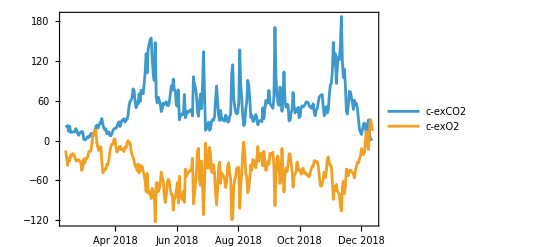

```mathematica
pcentroid= DateListPlot[tscentr, PlotLegends -> {"c-exCO2", "c-exO2"}]
```

#### stretch and width

```mathematica
swd = Table[Sqrt[5.991 Eigenvalues[Covariance[tsd[[d]]["Values"]]]], {d, ndays}];
```

```mathematica
stretchd = Transpose[swd][[1]];
```

```mathematica
widthd = Transpose[swd][[2]];
```

```mathematica
tsswd= TimeSeries[swd, {time}]
```

TimeSeries[…]

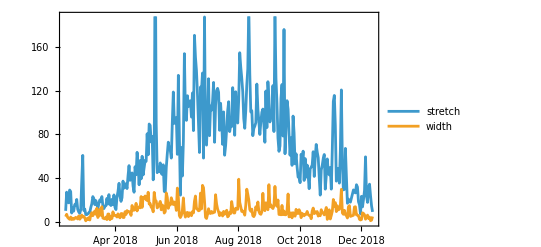

```mathematica
psw = DateListPlot[tsswd, PlotLegends -> {"stretch", "width"}]
```

#### slope and offset

```mathematica
sloped = Table[Eigenvectors[Covariance[tsd[[d]]["Values"]]][[1,2]]/Eigenvectors[Covariance[tsd[[d]]["Values"]]][[1,1]], {d, ndays}];
```

```mathematica
offsetd= Table[RegionDistance[oneline, centroidsd[[d]]], {d, ndays}];
```

```mathematica
slopoff = Transpose[{offsetd, sloped}];
```

```mathematica
tsso= TimeSeries[slopoff, {time}]
```

TimeSeries[…]

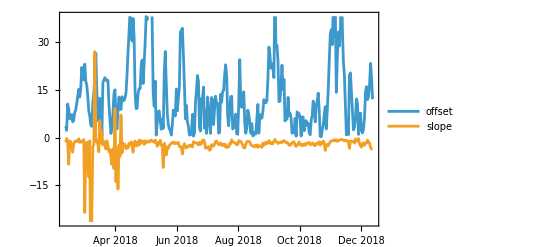

```mathematica
pso = DateListPlot[tsso, PlotLegends -> {"offset", "slope"}]
```

## Table of daily covariance parameters

MatrixForm is ready for file export

```mathematica
dlabels = Prepend[Drop[outlabels, 2], "date"]
```

{date,c-exCO2,c-exO2,stretch,width,offset,slope}

```mathematica
dcovpar = Prepend[Transpose[{time, cexCO2d, cexO2d, stretchd, widthd, offsetd, sloped }], dlabels]//MatrixForm
```

(date | c-exCO2 | c-exO2 | stretch | width | offset | slope
Sat 10 Feb 2018 12:00:00GMT+1 | 20.0753 | -15.0822 | 10.104 | 4.81082 | 3.53061 | -1.51756
Sun 11 Feb 2018 12:00:00GMT+1 | 21.7374 | -24.947 | 27.1694 | 6.95606 | 2.2695 | -0.338289
Mon 12 Feb 2018 12:00:00GMT+1 | 22.5487 | -37.4429 | 19.4109 | 4.15069 | 10.5318 | -0.803837
Tue 13 Feb 2018 12:00:00GMT+1 | 13.8439 | -26.6393 | 17.4149 | 3.13678 | 9.04776 | -8.37391
Wed 14 Feb 2018 12:00:00GMT+1 | 21.7325 | -30.0642 | 29.1162 | 2.36913 | 5.89146 | -1.13912
Thu 15 Feb 2018 12:00:00GMT+1 | 12.4133 | -21.6343 | 27.6728 | 4.43219 | 6.52027 | -1.25945
Fri 16 Feb 2018 12:00:00GMT+1 | 12.7849 | -23.0186 | 8.09225 | 2.16076 | 7.2363 | -2.68557
Sat 17 Feb 2018 12:00:00GMT+1 | 12.7439 | -19.741 | 13.0312 | 3.37453 | 4.94772 | -4.60711
Sun 18 Feb 2018 12:00:00GMT+1 | 13.0429 | -20.6497 | 9.83283 | 2.3137 | 5.37881 | -1.97585
Mon 19 Feb 2018 12:00:00GMT+1 | 13.0327 | -24.1888 | 15.7511 | 3.16416 | 7.88855 | -1.25865
Tue 20 Feb 2018 12:00:00GMT+1 | 17.9342 | -30.1444 | 14.8567 | 4.19915 | 8.63391 | -1.02325
Wed 21 Feb 2018 12:00:00GMT+1 | 15.8914 | -31.0587 | 20.5155 | 3.38728 | 10.7249 | -1.18195
Thu 22 Feb 2018 12:00:00GMT+1 | 10.2269 | -28.6059 | 11.4903 | 2.6717 | 12.9959 | -1.18552
Fri 23 Feb 2018 12:00:00GMT+1 | 7.92941 | -29.374 | 9.08758 | 5.46883 | 15.1636 | -0.367089
Sat 24 Feb 2018 12:00:00GMT+1 | 12.0932 | -30.1051 | 7.77807 | 2.4175 | 12.7363 | -1.50583
Sun 25 Feb 2018 12:00:00GMT+1 | 11.8712 | -33.6876 | 11.0929 | 3.8549 | 15.4265 | -1.4854
Mon 26 Feb 2018 12:00:00GMT+1 | 13.9785 | -45.1714 | 37.3713 | 6.2611 | 22.0567 | -1.10932
Tue 27 Feb 2018 12:00:00GMT+1 | 12.8751 | -40.6827 | 60.7842 | 4.4317 | 19.6629 | -1.28025
Wed 28 Feb 2018 12:00:00GMT+1 | 2.09305 | -27.7793 | 10.5432 | 5.07555 | 18.1629 | -0.655781
Thu 1 Mar 2018 12:00:00GMT+1 | 1.13246 | -33.7741 | 11.711 | 3.78509 | 23.0811 | -23.5569
Fri 2 Mar 2018 12:00:00GMT+1 | 1.46849 | -26.4864 | 6.71564 | 0.967113 | 17.6903 | -4.5732
Sat 3 Mar 2018 12:00:00GMT+1 | 4.44075 | -27.6973 | 6.626 | 2.88602 | 16.4449 | -1.42268
Sun 4 Mar 2018 12:00:00GMT+1 | 5.89113 | -24.1484 | 7.29316 | 2.11112 | 12.9098 | -8.53941
Mon 5 Mar 2018 12:00:00GMT+1 | 4.53653 | -16.3488 | 8.36204 | 4.00254 | 8.35252 | -12.3929
Tue 6 Mar 2018 12:00:00GMT+1 | 6.97978 | -16.5826 | 8.75394 | 1.737 | 6.79022 | -1.01929
Wed 7 Mar 2018 12:00:00GMT+1 | 10.1856 | -15.727 | 13.1952 | 6.56947 | 3.91838 | -56.2638
Thu 8 Mar 2018 12:00:00GMT+1 | 10.9204 | -5.94082 | 16.5423 | 8.50942 | 3.52108 | -24.7611
Fri 9 Mar 2018 12:00:00GMT+1 | 5.80954 | 9.53752 | 23.119 | 5.60968 | 10.852 | -2.84153
Sat 10 Mar 2018 12:00:00GMT+1 | 9.84882 | 9.907 | 21.2417 | 7.58475 | 13.9695 | -2.29276
Sun 11 Mar 2018 12:00:00GMT+1 | 13.5184 | 14.8811 | 15.8012 | 10.0127 | 20.0814 | 27.0013
Mon 12 Mar 2018 12:00:00GMT+1 | 21.4906 | 15.9922 | 19.4831 | 6.97449 | 26.5043 | -1.17918
Tue 13 Mar 2018 12:00:00GMT+1 | 23.2376 | -2.88998 | 16.3222 | 12.4678 | 14.388 | -0.728591
Wed 14 Mar 2018 12:00:00GMT+1 | 18.6066 | -10.6399 | 12.1296 | 4.01235 | 5.63326 | -2.12247
Thu 15 Mar 2018 12:00:00GMT+1 | 22.1968 | -14.9884 | 16.6054 | 6.15338 | 5.09717 | -4.47428
Fri 16 Mar 2018 12:00:00GMT+1 | 26.9941 | -9.51853 | 20.23 | 11.5075 | 12.3571 | 5.3483
Sat 17 Mar 2018 12:00:00GMT+1 | 25.796 | -9.87178 | 18.7476 | 6.02122 | 11.2601 | -1.67457
Sun 18 Mar 2018 12:00:00GMT+1 | 33.1714 | -33.9369 | 23.1445 | 13.9076 | 0.541295 | 2.11996
Mon 19 Mar 2018 12:00:00GMT+1 | 24.3649 | -48.6339 | 14.7434 | 3.50516 | 17.1608 | -2.356
Tue 20 Mar 2018 12:00:00GMT+1 | 18.9209 | -44.5753 | 12.1181 | 3.04947 | 18.1404 | -1.14398
Wed 21 Mar 2018 12:00:00GMT+1 | 15.8475 | -42.4872 | 14.243 | 2.80383 | 18.8371 | -2.11703
Thu 22 Mar 2018 12:00:00GMT+1 | 17.7658 | -43.5935 | 14.7572 | 4.42398 | 18.263 | -3.60079
Fri 23 Mar 2018 12:00:00GMT+1 | 10.1188 | -35.3486 | 21.4806 | 2.10606 | 17.8402 | -1.01766
Sat 24 Mar 2018 12:00:00GMT+1 | 11.01 | -36.5249 | 16.2987 | 7.18467 | 18.0418 | -2.45335
Sun 25 Mar 2018 12:00:00GMT+1 | 13.0599 | -28.0284 | 24.9355 | 7.19803 | 10.5843 | -4.43709
Mon 26 Mar 2018 12:00:00GMT+1 | 7.44098 | -15.5807 | 16.4447 | 1.95402 | 5.75566 | -3.84213
Tue 27 Mar 2018 12:00:00GMT+1 | 7.38198 | -9.17054 | 14.9315 | 4.78558 | 1.2647 | -6.03849
Wed 28 Mar 2018 12:00:00GMT+1 | 10.1883 | -5.28152 | 20.5601 | 3.13446 | 3.46962 | -8.44694
Thu 29 Mar 2018 12:00:00GMT+1 | 15.6378 | -5.06311 | 15.6647 | 9.21505 | 7.47744 | -3.52592
Fri 30 Mar 2018 12:00:00GMT+1 | 17.4578 | 2.00356 | 24.6557 | 5.86061 | 13.7612 | -9.75413
Sat 31 Mar 2018 12:00:00GMT+1 | 18.6233 | 2.61264 | 13.4326 | 6.06697 | 15.0161 | 9.10096
Sun 1 Apr 2018 12:00:00GMT+1 | 18.4466 | -9.96 | 11.2679 | 5.75791 | 6.00091 | -13.8925
Mon 2 Apr 2018 12:00:00GMT+1 | 21.159 | -17.3499 | 22.6009 | 4.44237 | 2.69347 | -3.41791
Tue 3 Apr 2018 12:00:00GMT+1 | 26.0963 | -13.6653 | 27.7012 | 7.3329 | 8.79008 | -16.1828
Wed 4 Apr 2018 13:30:00GMT+1 | 28.2599 | -10.2587 | 35.271 | 4.73977 | 12.7288 | -2.32509
Thu 5 Apr 2018 12:00:00GMT+1 | 21.1555 | -8.57447 | 23.3543 | 3.71862 | 8.89612 | -5.9167
Fri 6 Apr 2018 12:00:00GMT+1 | 26.0455 | -13.5167 | 18.7374 | 7.55889 | 8.85917 | 7.08237
Sat 7 Apr 2018 12:00:00GMT+1 | 30.5486 | -12.3775 | 22.0633 | 7.66767 | 12.8489 | -4.83227
Sun 8 Apr 2018 12:00:00GMT+1 | 31.2619 | -14.4337 | 37.2796 | 4.01692 | 11.8993 | -1.75105
Mon 9 Apr 2018 12:00:00GMT+1 | 32.8963 | -16.502 | 30.8144 | 4.02466 | 11.5925 | -2.61015
Tue 10 Apr 2018 12:00:00GMT+1 | 27.7588 | -10.1378 | 33.0995 | 9.27507 | 12.46 | -2.13148
Wed 11 Apr 2018 12:00:00GMT+1 | 31.345 | -11.3045 | 34.9439 | 6.78554 | 14.1708 | -3.51424
Thu 12 Apr 2018 12:00:00GMT+1 | 31.9594 | -4.01756 | 30.4608 | 10.3428 | 19.7579 | -2.83993
Fri 13 Apr 2018 12:00:00GMT+1 | 38.1179 | -0.134211 | 42.0705 | 8.98061 | 26.8585 | -3.24143
Sat 14 Apr 2018 12:00:00GMT+1 | 52.1652 | -5.27737 | 51.4403 | 9.43552 | 33.1547 | -1.81974
Sun 15 Apr 2018 12:00:00GMT+1 | 59.1431 | -3.11124 | 37.9749 | 8.88847 | 39.6205 | -2.30786
Mon 16 Apr 2018 12:00:00GMT+1 | 60.6356 | -14.7769 | 38.8696 | 5.92389 | 32.427 | -1.33284
Tue 17 Apr 2018 12:00:00GMT+1 | 64.8295 | -21.8807 | 44.751 | 14.9979 | 30.3694 | -2.5096
Wed 18 Apr 2018 12:00:00GMT+1 | 77.9769 | -25.0152 | 32.6987 | 10.6118 | 37.4496 | -4.60628
Thu 19 Apr 2018 12:00:00GMT+1 | 75.7064 | -30.5824 | 27.1044 | 10.6992 | 31.9074 | -1.70604
Fri 20 Apr 2018 12:00:00GMT+1 | 59.2401 | -38.8342 | 50.4454 | 12.0352 | 14.4292 | -1.10237
Sat 21 Apr 2018 12:00:00GMT+1 | 49.5319 | -36.6408 | 43.1351 | 16.9482 | 9.11532 | -2.63212
Sun 22 Apr 2018 12:00:00GMT+1 | 58.1619 | -45.1731 | 63.5933 | 10.0241 | 9.18449 | -1.49813
Mon 23 Apr 2018 12:00:00GMT+1 | 55.1115 | -35.513 | 51.8615 | 12.9906 | 13.8583 | -2.4641
Tue 24 Apr 2018 12:00:00GMT+1 | 70.3984 | -48.6798 | 33.9082 | 13.8062 | 15.3573 | -0.825953
Wed 25 Apr 2018 12:00:00GMT+1 | 58.6886 | -36.9264 | 56.0447 | 12.808 | 15.3882 | -2.11118
Thu 26 Apr 2018 12:00:00GMT+1 | 76.057 | -44.5087 | 39.2963 | 23.1708 | 22.308 | -0.928332
Fri 27 Apr 2018 12:00:00GMT+1 | 73.4261 | -38.9534 | 59.9596 | 13.2432 | 24.3758 | -1.36348
Sat 28 Apr 2018 12:00:00GMT+1 | 70.5177 | -46.467 | 42.915 | 22.4493 | 17.0064 | -1.22112
Sun 29 Apr 2018 12:00:00GMT+1 | 84.5367 | -51.7381 | 49.5907 | 21.8172 | 23.1921 | -2.15751
Mon 30 Apr 2018 12:00:00GMT+1 | 103.914 | -61.5937 | 56.2142 | 23.7068 | 29.9253 | -1.03154
Tue 1 May 2018 12:00:00GMT+1 | 130.896 | -77.0611 | 55.4167 | 20.2835 | 38.067 | -1.68757
Wed 2 May 2018 12:00:00GMT+1 | 101.878 | -49.4408 | 80.5307 | 19.5401 | 37.0784 | -1.20423
Thu 3 May 2018 12:00:00GMT+1 | 138.617 | -79.6874 | 61.3391 | 27.0855 | 41.6694 | -1.05531
Fri 4 May 2018 12:00:00GMT+1 | 145.387 | -76.2478 | 89.448 | 16.3571 | 48.8887 | -1.42141
Sat 5 May 2018 12:00:00GMT+1 | 151.885 | -78.1556 | 88.1971 | 16.7417 | 52.1347 | -1.24965
Sun 6 May 2018 12:00:00GMT+1 | 154.554 | -87.4822 | 72.9785 | 13.4005 | 47.4268 | -0.741365
Mon 7 May 2018 12:00:00GMT+1 | 123.047 | -72.0427 | 78.1401 | 12.7015 | 36.0653 | -1.09457
Tue 8 May 2018 12:00:00GMT+1 | 101.36 | -81.81 | 38.4373 | 9.21565 | 13.8239 | -1.25507
Wed 9 May 2018 12:00:00GMT+1 | 90.5789 | -76.6725 | 57.6351 | 26.9782 | 9.83329 | -1.50946
Thu 10 May 2018 12:00:00GMT+1 | 147.652 | -122.56 | 266.945 | 20.038 | 17.7425 | -0.759868
Fri 11 May 2018 12:00:00GMT+1 | 65.0895 | -63.982 | 89.6525 | 18.9694 | 0.783131 | -1.51936
Sat 12 May 2018 12:00:00GMT+1 | 56.6244 | -63.2768 | 44.9728 | 12.7532 | 4.70392 | -2.73811
Sun 13 May 2018 12:00:00GMT+1 | 65.4763 | -76.9949 | 49.1208 | 13.9377 | 8.14491 | -1.61223
Mon 14 May 2018 12:00:00GMT+1 | 61.1846 | -73.0482 | 45.9584 | 16.2866 | 8.38882 | -2.08093
Tue 15 May 2018 12:00:00GMT+1 | 55.9104 | -63.5403 | 53.8902 | 18.7283 | 5.39517 | -0.878963
Wed 16 May 2018 12:00:00GMT+1 | 43.6716 | -47.4144 | 44.4476 | 11.0224 | 2.64654 | -2.41468
Thu 17 May 2018 12:00:00GMT+1 | 48.6318 | -56.7646 | 43.2784 | 15.5439 | 5.75073 | -2.56337
Fri 18 May 2018 12:00:00GMT+1 | 56.5239 | -60.5952 | 52.1955 | 14.1066 | 2.87883 | -9.40613
Sat 19 May 2018 12:00:00GMT+1 | 54.5317 | -83.3405 | 27.8695 | 8.05796 | 20.3709 | -1.81208
Sun 20 May 2018 12:00:00GMT+1 | 54.9957 | -93.2599 | 27.4738 | 9.37155 | 27.0569 | -2.77993
Mon 21 May 2018 12:00:00GMT+1 | 58.5729 | -82.9707 | 49.8203 | 26.475 | 17.2519 | -5.44875
Tue 22 May 2018 12:00:00GMT+1 | 53.0342 | -64.0354 | 62.1582 | 22.4794 | 7.77901 | -3.06553
Wed 23 May 2018 12:00:00GMT+1 | 52.4185 | -58.3265 | 72.8605 | 12.378 | 4.17759 | -3.35427
Thu 24 May 2018 12:00:00GMT+1 | 57.3917 | -61.2438 | 66.6918 | 16.7318 | 2.72385 | -2.42982
Fri 25 May 2018 12:00:00GMT+1 | 70.1385 | -73.2691 | 65.3927 | 15.4338 | 2.21373 | -2.21948
Sat 26 May 2018 12:00:00GMT+1 | 82.2771 | -81.1581 | 58.3072 | 22.0514 | 0.791225 | -1.73648
Sun 27 May 2018 12:00:00GMT+1 | 75.9727 | -81.5019 | 90.995 | 18.9884 | 3.90975 | -1.59072
Mon 28 May 2018 12:00:00GMT+1 | 92.8316 | -105.009 | 118.726 | 15.8501 | 8.61104 | -1.45861
Tue 29 May 2018 12:00:00GMT+1 | 76.0047 | -87.372 | 90.0742 | 18.1794 | 8.03795 | -1.91696
Wed 30 May 2018 12:00:00GMT+1 | 75.3181 | -84.9479 | 92.3871 | 16.6557 | 6.80935 | -1.57101
Thu 31 May 2018 12:00:00GMT+1 | 53.4363 | -75.0337 | 95.333 | 10.4952 | 15.2717 | -1.83967
Fri 1 Jun 2018 12:00:00GMT+1 | 51.7157 | -63.6051 | 61.7659 | 30.9068 | 8.40706 | -1.79426
Sat 2 Jun 2018 12:00:00GMT+1 | 76.463 | -93.9461 | 133.973 | 22.0726 | 12.3624 | -1.51321
Sun 3 Jun 2018 12:00:00GMT+1 | 31.226 | -53.639 | 79.2198 | 5.75958 | 15.8483 | -2.82917
Mon 4 Jun 2018 12:00:00GMT+1 | 37.1104 | -84.0021 | 24.4223 | 3.95784 | 33.1575 | -2.77266
Tue 5 Jun 2018 12:00:00GMT+1 | 39.0119 | -86.6482 | 67.9763 | 5.88771 | 33.684 | -3.18195
Wed 6 Jun 2018 12:00:00GMT+1 | 40.6908 | -89.2941 | 41.9356 | 10.7473 | 34.3677 | -5.16296
Thu 7 Jun 2018 12:00:00GMT+1 | 39.4238 | -76.249 | 73.635 | 21.9357 | 26.0394 | -2.86118
Fri 8 Jun 2018 12:00:00GMT+1 | 69.4411 | -93.2378 | 153.773 | 8.4281 | 16.8268 | -1.9231
Sat 9 Jun 2018 12:00:00GMT+1 | 34.5322 | -42.871 | 99.8984 | 4.38813 | 5.89648 | -2.9358
Sun 10 Jun 2018 12:00:00GMT+1 | 39.6447 | -53.8637 | 92.7664 | 8.18769 | 10.0544 | -3.25397
Mon 11 Jun 2018 12:00:00GMT+1 | 44.0817 | -50.8528 | 115.321 | 8.70516 | 4.7879 | -2.7193
Tue 12 Jun 2018 12:00:00GMT+1 | 42.4687 | -47.6938 | 105.475 | 4.86443 | 3.69467 | -2.84726
Wed 13 Jun 2018 12:00:00GMT+1 | 45.1455 | -46.2237 | 110.221 | 8.30579 | 0.762415 | -2.31333
Thu 14 Jun 2018 12:00:00GMT+1 | 46.3185 | -44.0132 | 110.657 | 8.06478 | 1.63014 | -2.69283
Fri 15 Jun 2018 12:00:00GMT+1 | 45.9608 | -44.578 | 95.8228 | 5.65923 | 0.977831 | -2.42002
Sat 16 Jun 2018 12:00:00GMT+1 | 37.0248 | -26.6728 | 117.809 | 9.43243 | 7.32001 | -2.92985
Sun 17 Jun 2018 12:00:00GMT+1 | 96.193 | -95.5294 | 83.4096 | 8.19359 | 0.469265 | -1.30791
Mon 18 Jun 2018 12:00:00GMT+1 | 83.8612 | -81.9273 | 170.539 | 18.7578 | 1.36748 | -1.52852
Tue 19 Jun 2018 12:00:00GMT+1 | 80.4972 | -65.0479 | 150.553 | 23.6386 | 10.9243 | -1.58251
Wed 20 Jun 2018 12:00:00GMT+1 | 68.0084 | -47.0182 | 138.235 | 12.1462 | 14.8424 | -1.64201
Thu 21 Jun 2018 12:00:00GMT+1 | 43.8812 | -16.3169 | 116.921 | 11.4568 | 19.4909 | -2.09882
Fri 22 Jun 2018 12:00:00GMT+1 | 36.6084 | -11.6953 | 90.4356 | 10.1589 | 17.6162 | -2.28007
Sat 23 Jun 2018 12:00:00GMT+1 | 55.9773 | -60.2387 | 63.4303 | 10.4526 | 3.01323 | -1.49105
Sun 24 Jun 2018 12:00:00GMT+1 | 70.13 | -67.2728 | 123.272 | 26.2813 | 2.02037 | -2.16086
Mon 25 Jun 2018 12:00:00GMT+1 | 48.1486 | -30.7287 | 120.11 | 11.8386 | 12.3177 | -1.93044
Tue 26 Jun 2018 12:00:00GMT+1 | 81.8366 | -64.816 | 136.053 | 33.3973 | 12.0354 | -0.824864
Wed 27 Jun 2018 12:00:00GMT+1 | 134.016 | -111.526 | 58.312 | 31.2716 | 15.9024 | -0.740015
Thu 28 Jun 2018 12:00:00GMT+1 | 71.7104 | -67.5689 | 187.272 | 19.0452 | 2.9285 | -1.21999
Fri 29 Jun 2018 12:00:00GMT+1 | 15.558 | -3.5916 | 72.7897 | 4.17415 | 8.46153 | -3.35661
Sat 30 Jun 2018 12:00:00GMT+1 | 17.8823 | -19.763 | 70.1657 | 3.10285 | 1.32981 | -3.22448
Sun 1 Jul 2018 12:00:00GMT+1 | 23.4475 | -41.5151 | 94.6894 | 6.95675 | 12.7757 | -3.36671
Mon 2 Jul 2018 12:00:00GMT+1 | 27.8435 | -41.5454 | 130.86 | 12.0369 | 9.68872 | -2.80282
Tue 3 Jul 2018 12:00:00GMT+1 | 15.5491 | -10.2382 | 78.7845 | 8.07488 | 3.75535 | -4.02388
Wed 4 Jul 2018 12:00:00GMT+1 | 17.7844 | -19.6485 | 105.867 | 7.6281 | 1.31812 | -3.65036
Thu 5 Jul 2018 12:00:00GMT+1 | 29.7405 | -47.5649 | 102.114 | 9.56521 | 12.6038 | -2.22768
Fri 6 Jul 2018 12:00:00GMT+1 | 31.5553 | -48.46 | 110.163 | 8.05876 | 11.9534 | -2.63279
Sat 7 Jul 2018 12:00:00GMT+1 | 30.5202 | -36.2974 | 127.47 | 8.7144 | 4.08513 | -2.63935
Sun 8 Jul 2018 12:00:00GMT+1 | 36.1233 | -48.9122 | 72.7749 | 8.81429 | 9.04316 | -2.07389
Mon 9 Jul 2018 12:00:00GMT+1 | 61.4048 | -79.8047 | 106.532 | 24.8212 | 13.0107 | -1.21696
Tue 10 Jul 2018 12:00:00GMT+1 | 82.2079 | -96.8187 | 119.922 | 16.3581 | 10.3314 | -1.10164
Wed 11 Jul 2018 12:00:00GMT+1 | 59.2185 | -74.5039 | 122.041 | 11.78 | 10.8085 | -1.76511
Thu 12 Jul 2018 12:00:00GMT+1 | 37.987 | -39.9429 | 118.475 | 9.10782 | 1.38306 | -2.22464
Fri 13 Jul 2018 12:00:00GMT+1 | 30.2695 | -32.5353 | 83.7028 | 5.71694 | 1.60215 | -2.06055
Sat 14 Jul 2018 12:00:00GMT+1 | 45.2849 | -64.5525 | 108.421 | 8.38429 | 13.6242 | -1.68468
Sun 15 Jul 2018 12:00:00GMT+1 | 32.9938 | -48.627 | 91.7828 | 7.23992 | 11.0544 | -2.47012
Mon 16 Jul 2018 12:00:00GMT+1 | 30.5564 | -51.0625 | 70.8417 | 5.41681 | 14.5 | -2.19245
Tue 17 Jul 2018 12:00:00GMT+1 | 32.7731 | -53.6819 | 100.515 | 9.60546 | 14.7847 | -2.00749
Wed 18 Jul 2018 12:00:00GMT+1 | 29.4761 | -57.4467 | 60.9341 | 6.94301 | 19.7782 | -2.80028
Thu 19 Jul 2018 12:00:00GMT+1 | 38.2504 | -70.6363 | 70.0088 | 8.4601 | 22.9003 | -2.17852
Fri 20 Jul 2018 13:15:00GMT+1 | 34.6067 | -61.9628 | 85.8748 | 10.6399 | 19.3437 | -3.16402
Sat 21 Jul 2018 12:00:00GMT+1 | 27.9187 | -37.615 | 101.485 | 4.59221 | 6.85632 | -3.04313
Sun 22 Jul 2018 12:00:00GMT+1 | 28.24 | -33.4549 | 109.838 | 5.46803 | 3.68748 | -2.8788
Mon 23 Jul 2018 12:00:00GMT+1 | 36.5214 | -47.8756 | 82.5163 | 8.87599 | 8.02867 | -1.91986
Tue 24 Jul 2018 12:00:00GMT+1 | 39.769 | -57.9233 | 88.1132 | 7.54232 | 12.837 | -1.97182
Wed 25 Jul 2018 12:00:00GMT+1 | 100.735 | -119.085 | 87.1087 | 18.5979 | 12.9752 | -0.705378
Thu 26 Jul 2018 12:00:00GMT+1 | 114.275 | -118.091 | 122.709 | 12.7613 | 2.69817 | -1.29492
Fri 27 Jul 2018 12:00:00GMT+1 | 64.042 | -68.4078 | 109.135 | 8.19089 | 3.08709 | -1.52982
Sat 28 Jul 2018 12:00:00GMT+1 | 51.3312 | -59.0926 | 79.1776 | 8.12106 | 5.48814 | -1.59297
Sun 29 Jul 2018 12:00:00GMT+1 | 43.2775 | -53.6871 | 118.94 | 12.5353 | 7.36071 | -1.89236
Mon 30 Jul 2018 12:00:00GMT+1 | 40.0698 | -41.7581 | 103.877 | 12.0994 | 1.1938 | -2.26248
Tue 31 Jul 2018 12:00:00GMT+1 | 42.2541 | -40.7967 | 90.3541 | 11.4528 | 1.03055 | -2.18317
Wed 1 Aug 2018 12:00:00GMT+1 | 55.1394 | -40.189 | 112.113 | 39.0192 | 10.5715 | -0.990102
Thu 2 Aug 2018 12:00:00GMT+1 | 136.731 | -102.099 | 154.607 | 17.9542 | 24.4885 | -1.05295
Fri 3 Aug 2018 12:00:00GMT+1 | 86.048 | -69.0971 | 141.651 | 13.7847 | 11.9861 | -1.24479
Sat 4 Aug 2018 12:00:00GMT+1 | 62.6886 | -49.2555 | 131.522 | 9.55201 | 9.49865 | -1.67254
Sun 5 Aug 2018 12:00:00GMT+1 | 37.1012 | -18.2371 | 118.862 | 9.95678 | 13.3389 | -2.43076
Mon 6 Aug 2018 12:00:00GMT+1 | 22.6292 | -2.2634 | 94.4384 | 8.72698 | 14.4008 | -3.23189
Tue 7 Aug 2018 12:00:00GMT+1 | 25.3229 | -18.8415 | 85.5488 | 6.15081 | 4.58309 | -3.22073
Wed 8 Aug 2018 12:00:00GMT+1 | 47.6115 | -49.502 | 101.791 | 15.2611 | 1.3368 | -2.13835
Thu 9 Aug 2018 12:00:00GMT+1 | 58.9506 | -54.8276 | 124.777 | 29.8802 | 2.91539 | -1.39392
Fri 10 Aug 2018 12:00:00GMT+1 | 90.7053 | -78.5328 | 139.758 | 25.4369 | 8.60729 | -1.14895
Sat 11 Aug 2018 12:00:00GMT+1 | 82.7375 | -72.4542 | 195.767 | 20.0501 | 7.27141 | -1.18147
Sun 12 Aug 2018 12:00:00GMT+1 | 62.3929 | -55.8995 | 135.392 | 11.2496 | 4.59153 | -1.4
Mon 13 Aug 2018 12:00:00GMT+1 | 34.9011 | -36.8004 | 100.495 | 9.67759 | 1.34298 | -2.27967
Tue 14 Aug 2018 12:00:00GMT+1 | 38.4667 | -44.6679 | 101.65 | 11.6871 | 4.38493 | -2.48655
Wed 15 Aug 2018 12:00:00GMT+1 | 29.246 | -28.5221 | 78.8028 | 5.60705 | 0.511873 | -2.67414
Thu 16 Aug 2018 12:00:00GMT+1 | 28.895 | -29.9731 | 85.3815 | 4.82838 | 0.762341 | -2.91771
Fri 17 Aug 2018 12:00:00GMT+1 | 34.666 | -37.0089 | 87.5774 | 6.65322 | 1.65669 | -2.43199
Sat 18 Aug 2018 12:00:00GMT+1 | 39.3235 | -40.9415 | 90.7414 | 13.8279 | 1.14408 | -2.7611
Sun 19 Aug 2018 12:00:00GMT+1 | 34.4412 | -25.8764 | 125.985 | 11.262 | 6.05626 | -2.29149
Mon 20 Aug 2018 13:15:00GMT+1 | 23.7666 | -9.01305 | 102.751 | 18.2047 | 10.4324 | -3.05421
Tue 21 Aug 2018 12:00:00GMT+1 | 29.4562 | -31.4002 | 91.917 | 9.78787 | 1.3746 | -2.58032
Wed 22 Aug 2018 12:00:00GMT+1 | 29.8544 | -20.3924 | 79.9062 | 7.47867 | 6.69064 | -2.63103
Thu 23 Aug 2018 12:00:00GMT+1 | 29.7599 | -19.4808 | 91.5292 | 6.91554 | 7.26843 | -2.66874
Fri 24 Aug 2018 12:00:00GMT+1 | 28.4141 | -19.814 | 100.265 | 9.21871 | 6.08124 | -3.09075
Sat 25 Aug 2018 12:00:00GMT+1 | 49.6043 | -38.0381 | 103.131 | 26.1476 | 8.1785 | -1.74417
Sun 26 Aug 2018 12:00:00GMT+1 | 32.9418 | -16.0576 | 89.0247 | 12.6773 | 11.939 | -2.44412
Mon 27 Aug 2018 12:00:00GMT+1 | 47.5467 | -31.852 | 72.7871 | 10.2662 | 11.0978 | -2.03732
Tue 28 Aug 2018 12:00:00GMT+1 | 60.5589 | -45.1218 | 119.635 | 17.4763 | 10.9157 | -1.39846
Wed 29 Aug 2018 12:00:00GMT+1 | 56.1522 | -39.7434 | 86.1854 | 14.5378 | 11.6027 | -1.9231
Thu 30 Aug 2018 12:00:00GMT+1 | 57.6106 | -31.471 | 128.136 | 11.1026 | 18.4835 | -1.75942
Fri 31 Aug 2018 12:00:00GMT+1 | 75.7271 | -35.4797 | 113.016 | 34.0194 | 28.4592 | -0.961534
Sat 1 Sep 2018 12:00:00GMT+1 | 56.3915 | -19.3088 | 91.3265 | 13.7857 | 26.2214 | -1.34676
Sun 2 Sep 2018 12:00:00GMT+1 | 53.4244 | -22.558 | 96.8764 | 15.5932 | 21.8258 | -1.94021
Mon 3 Sep 2018 12:00:00GMT+1 | 51.3434 | -18.4725 | 95.3666 | 13.1412 | 23.2432 | -1.64933
Tue 4 Sep 2018 12:00:00GMT+1 | 48.5328 | -17.6823 | 124.578 | 12.1951 | 21.8146 | -1.96065
Wed 5 Sep 2018 12:00:00GMT+1 | 67.0635 | -40.4054 | 82.564 | 14.6467 | 18.8501 | -1.09902
Thu 6 Sep 2018 12:00:00GMT+1 | 170.501 | -98.1064 | 189.201 | 32.4395 | 51.1909 | -0.573788
Fri 7 Sep 2018 12:00:00GMT+1 | 95.0961 | -55.4192 | 131.119 | 17.2511 | 28.0558 | -1.22064
Sat 8 Sep 2018 12:00:00GMT+1 | 68.3839 | -27.3527 | 108.353 | 14.2354 | 29.0135 | -1.4176
Sun 9 Sep 2018 12:00:00GMT+1 | 57.2386 | -23.1814 | 76.6961 | 20.0297 | 24.0821 | -1.86413
Mon 10 Sep 2018 12:00:00GMT+1 | 53.071 | -37.1137 | 64.4837 | 6.7881 | 11.2835 | -1.56397
Tue 11 Sep 2018 12:00:00GMT+1 | 80.846 | -64.6799 | 69.3544 | 7.07972 | 11.4312 | -1.57037
Wed 12 Sep 2018 12:00:00GMT+1 | 74.6245 | -51.7068 | 112.971 | 6.4621 | 16.2053 | -1.36824
Thu 13 Sep 2018 12:00:00GMT+1 | 44.1264 | -11.9325 | 125.607 | 15.0536 | 22.7645 | -1.53945
Fri 14 Sep 2018 12:00:00GMT+1 | 70.6623 | -49.3114 | 78.4893 | 6.64888 | 15.0973 | -1.09509
Sat 15 Sep 2018 12:00:00GMT+1 | 103.374 | -77.51 | 175.851 | 9.93023 | 18.2884 | -0.999807
Sun 16 Sep 2018 12:00:00GMT+1 | 58.7747 | -51.3708 | 62.2962 | 6.45953 | 5.23537 | -1.25112
Mon 17 Sep 2018 12:00:00GMT+1 | 50.33 | -41.6989 | 88.3828 | 6.57103 | 6.10309 | -1.67051
Tue 18 Sep 2018 12:00:00GMT+1 | 54.6266 | -46.4441 | 110.775 | 10.354 | 5.78591 | -1.46511
Wed 19 Sep 2018 13:15:00GMT+1 | 54.1108 | -36.2342 | 102.876 | 25.4936 | 12.6407 | -1.8257
Thu 20 Sep 2018 12:00:00GMT+1 | 29.7277 | -20.0093 | 80.2519 | 4.53159 | 6.87201 | -2.35441
Fri 21 Sep 2018 12:00:00GMT+1 | 30.9529 | -20.0813 | 60.9283 | 5.49172 | 7.68743 | -2.43924
Sat 22 Sep 2018 12:00:00GMT+1 | 41.633 | -32.7194 | 76.8463 | 8.26047 | 6.30282 | -2.17018
Sun 23 Sep 2018 12:00:00GMT+1 | 46.7428 | -44.7937 | 51.6701 | 3.70443 | 1.37824 | -1.5933
Mon 24 Sep 2018 12:00:00GMT+1 | 72.5355 | -70.3819 | 96.7185 | 8.43637 | 1.52278 | -1.47998
Tue 25 Sep 2018 12:00:00GMT+1 | 51.2601 | -53.5062 | 81.3139 | 7.15722 | 1.5882 | -1.32727
Wed 26 Sep 2018 12:00:00GMT+1 | 41.7145 | -50.254 | 53.0577 | 5.21261 | 6.03836 | -2.39357
Thu 27 Sep 2018 12:00:00GMT+1 | 47.4737 | -46.8815 | 62.2382 | 11.4619 | 0.418747 | -2.79739
Fri 28 Sep 2018 12:00:00GMT+1 | 43.9118 | -32.4738 | 50.1108 | 7.88447 | 8.0879 | -2.30107
Sat 29 Sep 2018 12:00:00GMT+1 | 50.0165 | -39.4093 | 40.8877 | 7.5987 | 7.5004 | -2.00806
Sun 30 Sep 2018 12:00:00GMT+1 | 34.444 | -45.1503 | 40.9075 | 11.1359 | 7.57048 | -1.38007
Mon 1 Oct 2018 12:00:00GMT+1 | 36.3979 | -44.5609 | 35.8428 | 9.06112 | 5.77208 | -2.36556
Tue 2 Oct 2018 12:00:00GMT+1 | 49.9917 | -50.6566 | 61.7914 | 3.86043 | 0.470171 | -2.11296
Wed 3 Oct 2018 12:00:00GMT+1 | 52.301 | -43.0812 | 55.6728 | 7.8044 | 6.51938 | -2.52755
Thu 4 Oct 2018 12:00:00GMT+1 | 50.5649 | -41.4194 | 64.6654 | 6.69896 | 6.46682 | -2.09836
Fri 5 Oct 2018 12:00:00GMT+1 | 52.137 | -49.0931 | 37.8767 | 5.57369 | 2.15234 | -2.50302
Sat 6 Oct 2018 12:00:00GMT+1 | 54.6149 | -48.076 | 57.8745 | 6.99392 | 4.6237 | -1.89088
Sun 7 Oct 2018 12:00:00GMT+1 | 58.4351 | -50.8958 | 40.8526 | 6.85216 | 5.33107 | -2.29188
Mon 8 Oct 2018 12:00:00GMT+1 | 57.6543 | -52.3296 | 51.9333 | 9.55368 | 3.76511 | -1.80863
Tue 9 Oct 2018 12:00:00GMT+1 | 57.3829 | -51.0052 | 42.2524 | 6.85265 | 4.50966 | -1.61461
Wed 10 Oct 2018 12:00:00GMT+1 | 52.3255 | -54.5585 | 30.3425 | 5.85583 | 1.57896 | -1.56827
Thu 11 Oct 2018 12:00:00GMT+1 | 50.2984 | -49.0439 | 48.542 | 5.90976 | 0.887107 | -2.18229
Fri 12 Oct 2018 12:00:00GMT+1 | 51.0985 | -43.3951 | 49.9605 | 2.891 | 5.44709 | -2.26387
Sat 13 Oct 2018 12:00:00GMT+1 | 48.1883 | -38.4107 | 51.9726 | 9.9062 | 6.91387 | -1.76815
Sun 14 Oct 2018 12:00:00GMT+1 | 55.5471 | -39.2986 | 64.1416 | 12.6287 | 11.4894 | -1.75059
Mon 15 Oct 2018 13:15:00GMT+1 | 42.6147 | -30.262 | 41.5398 | 7.58692 | 8.73466 | -2.4898
Tue 16 Oct 2018 12:00:00GMT+1 | 37.5959 | -30.6235 | 58.6665 | 9.33976 | 4.93024 | -2.52002
Wed 17 Oct 2018 12:00:00GMT+1 | 46.3816 | -32.1282 | 70.7815 | 8.09455 | 10.0786 | -1.90407
Thu 18 Oct 2018 12:00:00GMT+1 | 47.6042 | -31.4683 | 63.8175 | 9.49883 | 11.4098 | -2.0578
Fri 19 Oct 2018 12:00:00GMT+1 | 57.3955 | -37.6318 | 58.6984 | 5.28383 | 13.9751 | -1.56447
Sat 20 Oct 2018 12:00:00GMT+1 | 65.6207 | -53.7426 | 40.8405 | 6.97908 | 8.39908 | -1.31041
Sun 21 Oct 2018 12:00:00GMT+1 | 67.7449 | -67.1798 | 24.4848 | 5.59519 | 0.399614 | -2.40869
Mon 22 Oct 2018 12:00:00GMT+1 | 68.5889 | -68.9638 | 47.4163 | 11.1353 | 0.265123 | -1.49909
Tue 23 Oct 2018 12:00:00GMT+1 | 69.3825 | -65.9129 | 51.6971 | 8.81689 | 2.45337 | -1.89253
Wed 24 Oct 2018 12:00:00GMT+1 | 50.4775 | -56.0794 | 58.0022 | 7.92087 | 3.96118 | -1.07845
Thu 25 Oct 2018 12:00:00GMT+1 | 37.2793 | -47.5705 | 61.6078 | 6.40537 | 7.27698 | -1.64517
Fri 26 Oct 2018 12:00:00GMT+1 | 42.2057 | -55.9224 | 29.923 | 9.81841 | 9.69918 | -4.0525
Sat 27 Oct 2018 12:00:00GMT+1 | 51.1687 | -47.3626 | 42.2713 | 13.1842 | 2.69135 | -2.35778
Sun 28 Oct 2018 12:00:00GMT+1 | 41.3899 | -29.3598 | 57.5667 | 2.29596 | 8.50657 | -2.17156
Mon 29 Oct 2018 12:00:00GMT+1 | 46.4591 | -24.5148 | 45.8006 | 6.10522 | 15.517 | -2.56422
Tue 30 Oct 2018 12:00:00GMT+1 | 68.3869 | -33.6647 | 42.9761 | 11.069 | 24.5523 | -1.91076
Wed 31 Oct 2018 12:00:00GMT+1 | 83.3071 | -37.44 | 49.8091 | 2.65281 | 32.4329 | -1.25549
Thu 1 Nov 2018 12:00:00GMT+1 | 86.2367 | -38.2551 | 29.9349 | 5.94068 | 33.9281 | -1.10254
Fri 2 Nov 2018 12:00:00GMT+1 | 102.519 | -61.1789 | 66.7987 | 9.77252 | 29.2316 | -1.03053
Sat 3 Nov 2018 12:00:00GMT+1 | 147.935 | -88.6135 | 110.06 | 20.4926 | 41.9468 | -1.00839
Sun 4 Nov 2018 12:00:00GMT+1 | 113.865 | -69.0236 | 115.579 | 14.1708 | 31.7076 | -0.702748
Mon 5 Nov 2018 12:00:00GMT+1 | 130.834 | -75.2929 | 87.9455 | 17.6137 | 39.2732 | -0.929913
Tue 6 Nov 2018 12:00:00GMT+1 | 86.2241 | -66.12 | 37.2391 | 9.39862 | 14.2158 | -0.693767
Wed 7 Nov 2018 12:00:00GMT+1 | 111.319 | -75.465 | 48.466 | 14.7659 | 25.3526 | -1.21667
Thu 8 Nov 2018 12:00:00GMT+1 | 125.802 | -78.8047 | 48.677 | 11.0083 | 33.2319 | -0.91934
Fri 9 Nov 2018 12:00:00GMT+1 | 121.881 | -81.1863 | 35.4411 | 11.5297 | 28.7755 | -0.836773
Sat 10 Nov 2018 12:00:00GMT+1 | 144.098 | -98.7287 | 65.1528 | 14.8164 | 32.0809 | -0.712717
Sun 11 Nov 2018 12:00:00GMT+1 | 187.069 | -106.18 | 120.612 | 29.8134 | 57.1977 | -0.591998
Mon 12 Nov 2018 12:00:00GMT+1 | 118.996 | -70.1128 | 53.2438 | 8.18051 | 34.5654 | -0.612605
Tue 13 Nov 2018 12:00:00GMT+1 | 95.1295 | -61.266 | 29.2597 | 6.92478 | 23.9451 | -0.836287
Wed 14 Nov 2018 12:00:00GMT+1 | 107.742 | -79.9899 | 29.7291 | 10.5951 | 19.6236 | -1.00475
Thu 15 Nov 2018 12:00:00GMT+1 | 82.59 | -68.2297 | 67.1897 | 6.77023 | 10.1543 | -0.808018
Fri 16 Nov 2018 12:00:00GMT+1 | 44.0396 | -42.8274 | 41.555 | 5.67765 | 0.85715 | -0.879241
Sat 17 Nov 2018 12:00:00GMT+1 | 39.9262 | -45.1278 | 17.0269 | 3.56718 | 3.67805 | -1.24079
Sun 18 Nov 2018 12:00:00GMT+1 | 54.2936 | -52.9374 | 20.7901 | 13.8126 | 0.958948 | -1.22847
Mon 19 Nov 2018 12:00:00GMT+1 | 74.1256 | -46.3734 | 18.4861 | 14.8841 | 19.6237 | -3.39438
Tue 20 Nov 2018 12:00:00GMT+1 | 73.3701 | -44.6049 | 18.0513 | 5.00732 | 20.34 | -1.08539
Fri 23 Nov 2018 12:00:00GMT+1 | 47.0339 | -50.4346 | 29.2276 | 6.06161 | 2.40468 | -1.297
Sat 24 Nov 2018 12:00:00GMT+1 | 60.8973 | -56.3302 | 27.2403 | 13.6422 | 3.22939 | -1.78901
Sun 25 Nov 2018 12:00:00GMT+1 | 53.9149 | -45.3033 | 26.4844 | 13.8196 | 6.08936 | -0.447456
Mon 26 Nov 2018 12:00:00GMT+1 | 55.9268 | -38.7277 | 33.9606 | 6.40793 | 12.1616 | -1.12604
Tue 27 Nov 2018 12:00:00GMT+1 | 47.76 | -32.6318 | 31.8676 | 6.13775 | 10.6973 | -0.954516
Wed 28 Nov 2018 12:00:00GMT+1 | 32.4134 | -33.7928 | 18.4604 | 5.65739 | 0.975386 | -0.307613
Thu 29 Nov 2018 12:00:00GMT+1 | 17.1118 | -27.841 | 15.6497 | 2.31733 | 7.5867 | -1.76936
Fri 30 Nov 2018 12:00:00GMT+1 | 12.2819 | -23.1094 | 7.35682 | 1.77774 | 7.65619 | -2.55374
Sat 1 Dec 2018 12:00:00GMT+1 | 9.18194 | -12.0064 | 23.3884 | 2.15235 | 1.99722 | -3.01113
Sun 2 Dec 2018 12:00:00GMT+1 | 17.2884 | -15.2431 | 13.7145 | 8.30929 | 1.44628 | -1.98897
Mon 3 Dec 2018 12:00:00GMT+1 | 24.8267 | -21.1167 | 20.5205 | 7.69553 | 2.6234 | -1.61612
Tue 4 Dec 2018 12:00:00GMT+1 | 26.2565 | -17.1766 | 28.6031 | 6.50267 | 6.42046 | -2.44024
Wed 5 Dec 2018 12:00:00GMT+1 | 18.2546 | 2.14248 | 59.4483 | 2.43156 | 14.4229 | -1.86997
Thu 6 Dec 2018 12:00:00GMT+1 | 8.67324 | 13.9782 | 23.6867 | 4.1737 | 16.017 | -1.5513
Fri 7 Dec 2018 12:00:00GMT+1 | 25.035 | -8.10089 | 17.8052 | 6.22393 | 11.9742 | -0.765498
Sat 8 Dec 2018 12:00:00GMT+1 | 31.2604 | -13.2793 | 31.4537 | 3.09852 | 12.7146 | -1.62141
Sun 9 Dec 2018 12:00:00GMT+1 | 9.99083 | 13.4295 | 34.4785 | 4.41594 | 16.5607 | -1.67513
Mon 10 Dec 2018 12:00:00GMT+1 | 1.33025 | 31.6829 | 23.7421 | 1.13047 | 23.3438 | -3.06294
Tue 11 Dec 2018 12:00:00GMT+1 | 1.82471 | 24.4728 | 14.6372 | 1.59889 | 18.5951 | -3.59961
Wed 12 Dec 2018 12:00:00GMT+1 | 2.18261 | 14.8348 | 9.1519 | 4.90641 | 12.0331 | -3.65796)

## Monthly averages of the 24 - h cycles

## developing the analysis procedure for one month

extract June data in the useful format "DatePath"

```mathematica
tx1 = tsm[[5]]["DatePath"]
```

appends the integer "Hour" to the first record

```mathematica
tx11 = Append[tx1[[1]], DateValue[tx1[[1,1]], "Hour"]]
```

{Fri 1 Jun 2018 00:00:00GMT+1,{36.7785,-52.7283},0}

```mathematica
tx2 = Table[Append[tx1[[t]], DateValue[tx1[[t,1]], "Hour"]], {t, Length[tx1]}]
```

reformat the data for easy selection of records - pattern {CO2, O2, Hour}

```mathematica
tx3 = Table[{tx2[[t, 2]][[1]], tx2[[t, 2]][[2]], tx2[[t,3]]}, {t, Length[tx2]}]
```

extract 24 lists for each hour

```mathematica
tx4 = Table[Select[tx3, MemberQ[#, h]&] ,{h, 0, 23}]
```

calculate the monthly Means for all 24 hours

```mathematica
tx5 = Table[Mean[tx4[[h1]]], {h1, 24}]
```

{{60.072,-68.6237,0},{64.6352,-79.2485,1},{67.1142,-84.5266,2},{70.9989,-92.0702,3},{73.3048,-97.484,4},{75.0332,-100.561,5},{73.0355,-101.181,6},{70.6302,-98.535,7},{65.982,-91.6036,8},{61.6195,-84.1336,9},{57.3293,-74.8378,10},{52.4006,-62.3556,11},{48.,-48.7352,12},{42.7763,-33.0458,13},{39.0866,-21.8258,14},{38.1519,-17.0967,15},{35.3322,-9.58284,16},{33.7051,-6.20369,17},{35.0994,-12.575,18},{37.3392,-20.2104,19},{41.6663,-30.3641,20},{47.532,-40.9011,21},{52.3762,-52.8068,22},{56.4898,-61.3991,23}}

condense the last steps to one line of code

```mathematica
tx6 = Table[Mean[Table[Select[Table[{tx2[[t, 2]][[1]], tx2[[t, 2]][[2]], tx2[[t,3]]}, {t, Length[tx2]}], 
MemberQ[#, h]&] ,{h, 0, 23}][[h1]]], {h1, 24}]
```

{{60.072,-68.6237,0},{64.6352,-79.2485,1},{67.1142,-84.5266,2},{70.9989,-92.0702,3},{73.3048,-97.484,4},{75.0332,-100.561,5},{73.0355,-101.181,6},{70.6302,-98.535,7},{65.982,-91.6036,8},{61.6195,-84.1336,9},{57.3293,-74.8378,10},{52.4006,-62.3556,11},{48.,-48.7352,12},{42.7763,-33.0458,13},{39.0866,-21.8258,14},{38.1519,-17.0967,15},{35.3322,-9.58284,16},{33.7051,-6.20369,17},{35.0994,-12.575,18},{37.3392,-20.2104,19},{41.6663,-30.3641,20},{47.532,-40.9011,21},{52.3762,-52.8068,22},{56.4898,-61.3991,23}}

### example: plot 24 hour averages for June

rearrange results

```mathematica
hours = Transpose[tx6][[3]]+ 0.5
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5}

```mathematica
avCO2 = Transpose[tx6][[1]]
```

{60.072,64.6352,67.1142,70.9989,73.3048,75.0332,73.0355,70.6302,65.982,61.6195,57.3293,52.4006,48.,42.7763,39.0866,38.1519,35.3322,33.7051,35.0994,37.3392,41.6663,47.532,52.3762,56.4898}

```mathematica
avO2 = Transpose[tx6][[2]]
```

{-68.6237,-79.2485,-84.5266,-92.0702,-97.484,-100.561,-101.181,-98.535,-91.6036,-84.1336,-74.8378,-62.3556,-48.7352,-33.0458,-21.8258,-17.0967,-9.58284,-6.20369,-12.575,-20.2104,-30.3641,-40.9011,-52.8068,-61.3991}

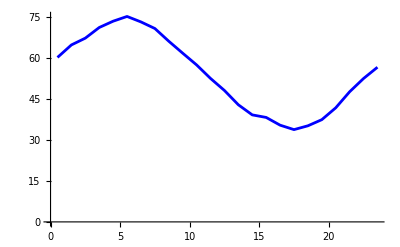

```mathematica
pCO2 = ListPlot[Transpose[{hours,avCO2}], Joined -> True, PlotStyle -> Blue]
```

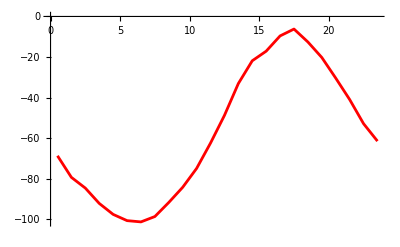

```mathematica
pO2 = ListPlot[Transpose[{hours,avO2}], Joined -> True, PlotStyle -> Red]
```

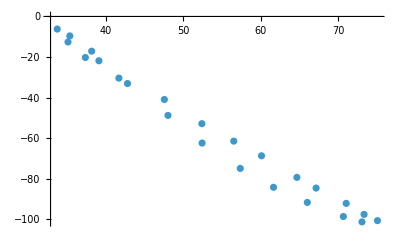

```mathematica
pcycle = ListPlot[Transpose[{avCO2, avO2}]]
```

## Calculate 24-h averages for all months

### Preparing data structure and averaging

```mathematica
tx24= Table[Table[Append[tsm[[m]]["DatePath"][[t]], DateValue[tsm[[m]]["DatePath"][[t,1]], "Hour"]], {t, tsm[[m]]["PathLength"]}], {m, nm}]
```

mapping the example above for all 24h-data of all months m and calculating the Mean

```mathematica
mtx24 = Table[Table[Mean[Table[Select[Table[{tx24[[m,t,3]],tx24[[m,t, 2]][[1]], tx24[[m,t, 2]][[2]] }, {t, Length[tx24[[m]]]}], 
MemberQ[#, h]&] ,{h, 0, 23}][[h1]]], {h1, 24}], {m,nm}]
```

{{{0,14.0672,-26.5374},{1,14.8162,-27.7599},{2,16.247,-30.0091},{3,16.2457,-30.7037},{4,16.5359,-31.52},{5,16.1026,-31.6055},{6,16.1369,-32.6735},{7,15.998,-33.2086},{8,15.9934,-33.3761},{9,14.6533,-31.8527},{10,13.7926,-30.3057},{11,13.5999,-29.069},{12,13.37,-27.8064},{13,14.0594,-27.4405},{14,13.8663,-26.4648},{15,14.2159,-25.5788},{16,13.6008,-25.1471},{17,12.4473,-24.3221},{18,12.9105,-24.7892},{19,12.124,-24.1783},{20,11.8296,-24.1042},{21,12.6795,-25.2362},{22,13.1567,-25.8769},{23,13.202,-26.0836}},{{0,13.4459,-15.8971},{1,13.9421,-17.8632},{2,13.3103,-17.722},{3,13.5512,-18.8802},{4,13.3733,-19.5563},{5,13.7257,-20.8625},{6,14.2007,-21.7527},{7,14.6879,-22.5196},{8,14.3342,-22.3537},{9,14.1002,-21.24},{10,15.1965,-21.303},{11,15.1545,-19.8391},{12,15.3182,-17.9861},{13,15.0933,-15.6552},{14,14.7325,-13.7399},{15,14.1402,-11.9305},{16,13.5418,-10.3914},{17,13.5016,-10.1176},{18,13.1224,-10.3447},{19,12.8922,-10.8507},{20,13.3274,-11.964},{21,13.2576,-12.1496},{22,14.19,-14.0371},{23,13.8934,-14.26}},{{0,49.3813,-26.591},{1,50.3929,-29.7224},{2,51.9664,-32.9101},{3,52.9192,-34.9519},{4,56.7391,-40.3577},{5,56.0383,-40.6842},{6,54.8024,-40.3076},{7,54.3722,-40.2602},{8,53.3174,-38.0352},{9,52.234,-34.9427},{10,52.8557,-31.7749},{11,51.5086,-27.004},{12,48.6764,-19.772},{13,47.1356,-14.1781},{14,46.4134,-9.93812},{15,44.8707,-5.75299},{16,45.5917,-5.59245},{17,46.7952,-6.80856},{18,47.9393,-9.56853},{19,50.5935,-14.5724},{20,49.5433,-15.8107},{21,49.7729,-18.9439},{22,49.5817,-20.9308},{23,49.8453,-23.9756}},{{0,91.3621,-85.4125},{1,92.2179,-90.1537},{2,94.0757,-94.9185},{3,93.303,-96.0298},{4,94.2219,-98.7697},{5,93.5738,-100.766},{6,94.9839,-102.53},{7,93.5385,-100.207},{8,89.8087,-94.7223},{9,83.8278,-86.6004},{10,81.7791,-80.4787},{11,81.4002,-74.7349},{12,84.738,-70.8387},{13,78.1473,-58.8189},{14,74.0178,-51.0242},{15,70.1344,-44.6904},{16,69.9286,-43.6224},{17,70.6893,-44.9726},{18,74.4451,-52.0935},{19,75.541,-56.6061},{20,80.3171,-64.3277},{21,81.5112,-68.8008},{22,82.0002,-71.901},{23,83.5298,-76.3579}},{{0,60.072,-68.6237},{1,64.6352,-79.2485},{2,67.1142,-84.5266},{3,70.9989,-92.0702},{4,73.3048,-97.484},{5,75.0332,-100.561},{6,73.0355,-101.181},{7,70.6302,-98.535},{8,65.982,-91.6036},{9,61.6195,-84.1336},{10,57.3293,-74.8378},{11,52.4006,-62.3556},{12,48.,-48.7352},{13,42.7763,-33.0458},{14,39.0866,-21.8258},{15,38.1519,-17.0967},{16,35.3322,-9.58284},{17,33.7051,-6.20369},{18,35.0994,-12.575},{19,37.3392,-20.2104},{20,41.6663,-30.3641},{21,47.532,-40.9011},{22,52.3762,-52.8068},{23,56.4898,-61.3991}},{{0,38.6291,-52.623},{1,43.8639,-65.2452},{2,48.2591,-74.6206},{3,52.8884,-83.793},{4,56.5806,-90.1299},{5,59.5119,-94.379},{6,62.0257,-97.6839},{7,59.1598,-92.9527},{8,59.8542,-92.4657},{9,57.3948,-86.3259},{10,51.6967,-76.1652},{11,48.2804,-67.687},{12,41.9772,-55.4227},{13,39.0046,-45.2466},{14,33.6974,-30.0907},{15,30.9903,-22.4017},{16,26.2916,-11.6394},{17,25.5156,-11.4704},{18,26.7306,-14.2604},{19,28.0854,-19.5943},{20,29.0325,-23.1003},{21,33.0714,-33.8075},{22,32.8325,-36.8093},{23,34.092,-41.3255}},{{0,52.4816,-41.4088},{1,56.8203,-50.9451},{2,60.2693,-60.4766},{3,60.9027,-65.7971},{4,65.2962,-74.1183},{5,70.1578,-82.0447},{6,74.8689,-90.4997},{7,72.8243,-88.8962},{8,66.6861,-81.4769},{9,62.4452,-69.7166},{10,60.9422,-62.4595},{11,52.5268,-47.2595},{12,45.4153,-31.5408},{13,40.7833,-21.5391},{14,33.4459,-6.20322},{15,29.6088,3.02319},{16,27.4706,9.42363},{17,25.7269,13.4805},{18,25.9898,10.6891},{19,28.8723,3.56929},{20,33.5346,-6.23219},{21,40.6588,-19.0504},{22,47.3121,-30.4232},{23,50.3678,-35.5071}},{{0,59.9745,-43.1437},{1,61.921,-47.3474},{2,67.7078,-55.9986},{3,74.1702,-64.1425},{4,78.2785,-70.0437},{5,82.1944,-74.1519},{6,85.7807,-78.8355},{7,86.6835,-81.4454},{8,83.8398,-77.8663},{9,79.28,-69.4072},{10,68.6469,-54.6998},{11,59.9324,-44.1791},{12,54.2138,-34.0709},{13,50.378,-25.6137},{14,47.1125,-17.9119},{15,41.6575,-9.22036},{16,39.7388,-4.15817},{17,38.7349,-3.72686},{18,40.8151,-9.78139},{19,41.9931,-13.7494},{20,44.1612,-18.8276},{21,48.0828,-26.2231},{22,51.0133,-33.0219},{23,56.2314,-39.6}},{{0,54.6808,-50.0381},{1,58.0776,-54.6246},{2,60.5366,-58.4975},{3,61.149,-60.6374},{4,62.1437,-63.2519},{5,63.0376,-65.1219},{6,62.6111,-65.8995},{7,62.9153,-68.145},{8,61.5558,-65.724},{9,58.5966,-60.199},{10,54.2777,-52.4114},{11,52.4275,-45.2158},{12,48.9954,-36.8225},{13,45.6006,-29.6967},{14,43.7433,-23.74},{15,41.9248,-19.6127},{16,40.7518,-18.1013},{17,41.9747,-21.3812},{18,44.9898,-27.6524},{19,47.913,-32.9931},{20,50.1736,-37.6305},{21,51.2917,-40.1183},{22,53.6434,-44.1427},{23,55.167,-47.0568}},{{0,81.7009,-57.9394},{1,85.2121,-61.0195},{2,85.4901,-62.1924},{3,87.0963,-64.0634},{4,91.1102,-67.1555},{5,92.7359,-68.3716},{6,92.2307,-68.4187},{7,93.4582,-70.5556},{8,94.2488,-71.7584},{9,95.0686,-72.1889},{10,93.7885,-69.6838},{11,90.1809,-64.7473},{12,88.2633,-60.6238},{13,82.1579,-54.4671},{14,76.1531,-47.5573},{15,72.5315,-43.6261},{16,72.1443,-43.6806},{17,72.8332,-45.115},{18,76.1417,-47.9772},{19,79.6658,-51.5807},{20,80.2142,-52.6969},{21,79.8002,-53.6869},{22,79.4129,-55.1763},{23,78.3651,-55.8785}},{{0,15.6947,-2.42664},{1,15.4694,-2.77498},{2,15.8678,-4.88719},{3,15.1874,-5.12756},{4,14.6732,-4.69742},{5,15.047,-5.74256},{6,15.2069,-5.49808},{7,15.066,-5.05089},{8,15.0404,-4.18463},{9,14.294,-2.73481},{10,13.3077,0.738177},{11,11.6996,4.93997},{12,11.4677,7.0238},{13,12.221,7.65535},{14,12.576,8.00615},{15,12.6942,8.57058},{16,12.8352,8.43332},{17,13.2142,7.18052},{18,14.1415,5.20375},{19,14.0973,4.60624},{20,14.3729,4.63166},{21,14.6962,4.49052},{22,15.7998,2.33824},{23,15.8651,0.562379}}}

```mathematica
tco2 = Table[Table[{mtx24[[m, h,1]] + 0.5, mtx24[[m,h, 2]]}, {h,24}], {m, nm}];
```

```mathematica
to2 =Table[Table[{mtx24[[m, h,1]] + 0.5, mtx24[[m,h, 3]]}, {h,24}], {m, nm}];
```

#### cycles

```mathematica
co2o2 = Table[Table[{mtx24[[m, h,2]], mtx24[[m,h, 3]]}, {h,24}], {m, nm}];
```

### Ploting daily averages

#### exCO2

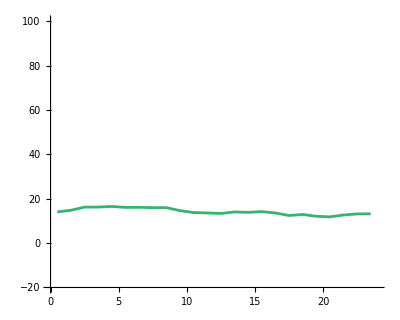
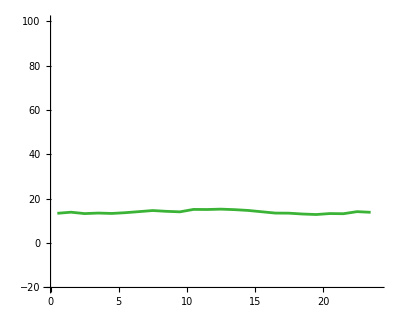
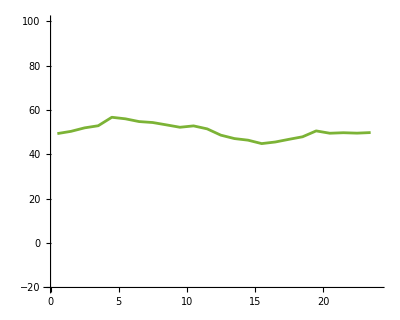
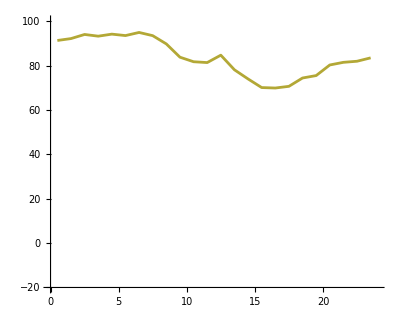
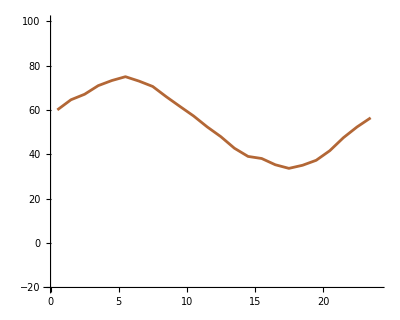
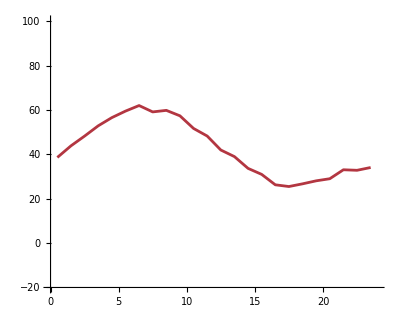
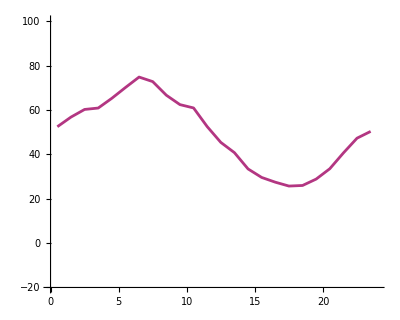
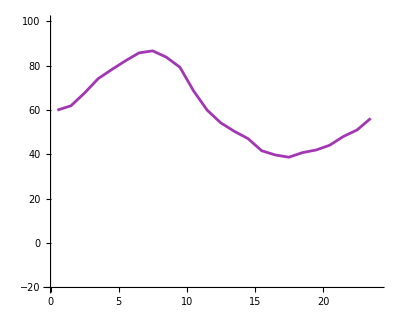

```mathematica
ptco2x = Table[ListLinePlot[tco2[[m]], PlotRange -> {{0,24},{ -20, 100}}, AspectRatio -> 0.8, AxesOrigin -> {0, -20},  PlotStyle -> col[[m]]], {m, nm}]
```

```mathematica
coltab
```

Feb | Mar | Apr | May | Jun | Jul | Aug | Sep | Oct | Nov | Dec
RGBColor[0.21176470588235294, 0.7019607843137254, 0.4392156862745098] | RGBColor[0.23137254901960785, 0.7019607843137254, 0.21176470588235294] | RGBColor[0.48627450980392156, 0.7019607843137254, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.6588235294117647, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.403921568627451, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.21176470588235294, 0.2549019607843137] | RGBColor[0.7019607843137254, 0.21176470588235294, 0.5098039215686274] | RGBColor[0.6352941176470588, 0.21176470588235294, 0.7019607843137254] | RGBColor[0.3843137254901961, 0.21176470588235294, 0.7019607843137254] | RGBColor[0.21176470588235294, 0.2901960784313726, 0.7019607843137254] | RGBColor[0.21176470588235294, 0.5450980392156862, 0.7019607843137254]

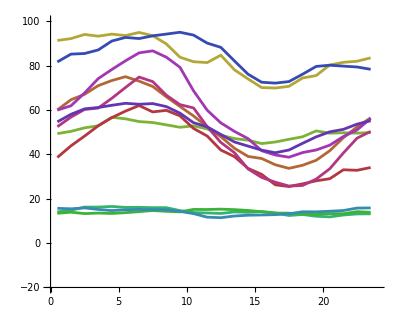

```mathematica
sco2 = Show[ptco2x]
```

#### exO2

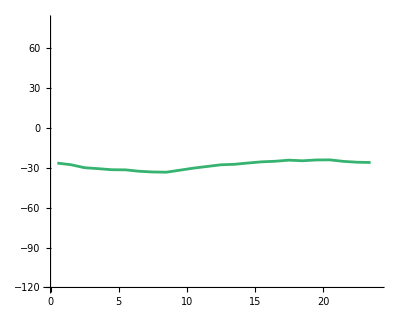
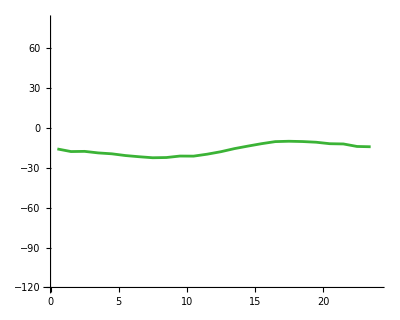
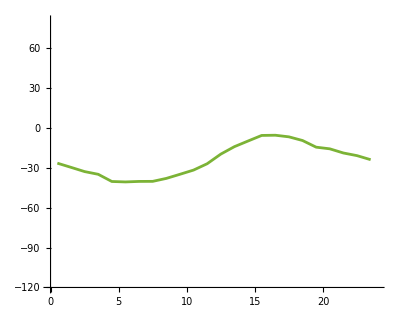
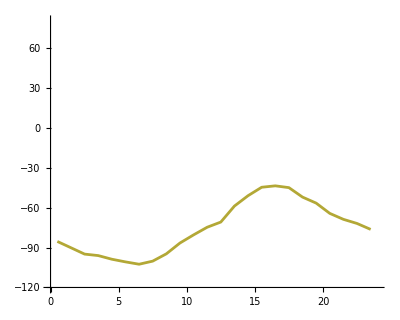
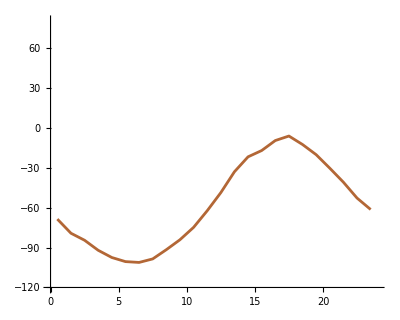
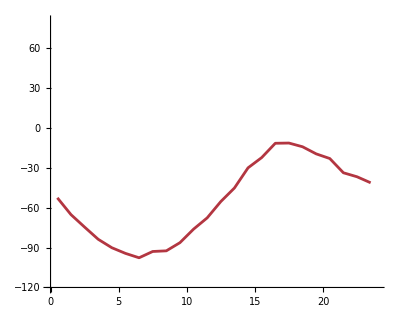
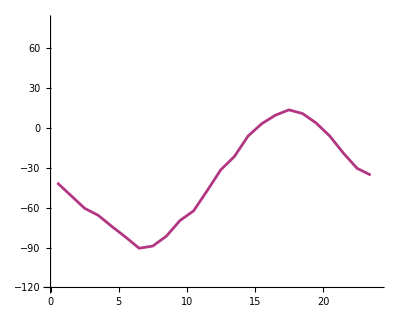
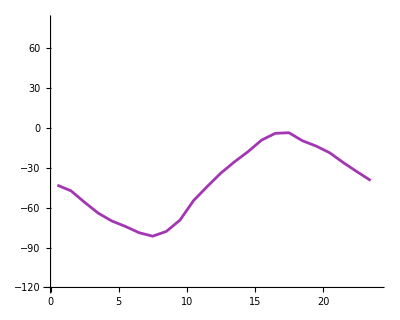

```mathematica
pto2x = Table[ListLinePlot[to2[[m]], PlotRange -> {{0,24},{ -120, 80}}, AspectRatio -> 0.8, AxesOrigin -> {0, -120},  PlotStyle -> col[[m]]], {m, nm}]
```

```mathematica
coltab
```

Feb | Mar | Apr | May | Jun | Jul | Aug | Sep | Oct | Nov | Dec
RGBColor[0.21176470588235294, 0.7019607843137254, 0.4392156862745098] | RGBColor[0.23137254901960785, 0.7019607843137254, 0.21176470588235294] | RGBColor[0.48627450980392156, 0.7019607843137254, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.6588235294117647, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.403921568627451, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.21176470588235294, 0.2549019607843137] | RGBColor[0.7019607843137254, 0.21176470588235294, 0.5098039215686274] | RGBColor[0.6352941176470588, 0.21176470588235294, 0.7019607843137254] | RGBColor[0.3843137254901961, 0.21176470588235294, 0.7019607843137254] | RGBColor[0.21176470588235294, 0.2901960784313726, 0.7019607843137254] | RGBColor[0.21176470588235294, 0.5450980392156862, 0.7019607843137254]

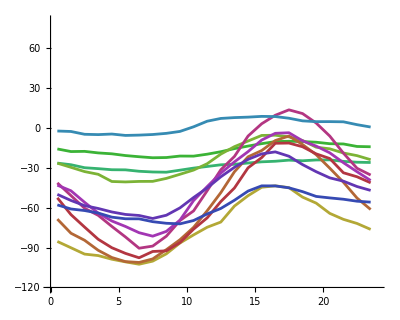

```mathematica
so2 = Show[pto2x]
```

#### 24 - h cycles

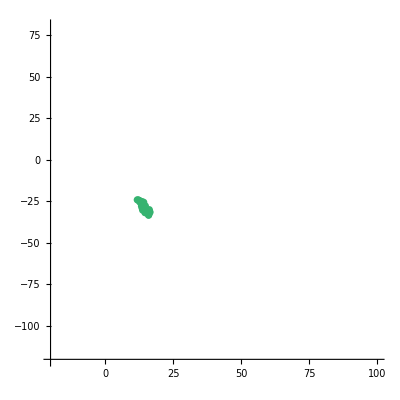
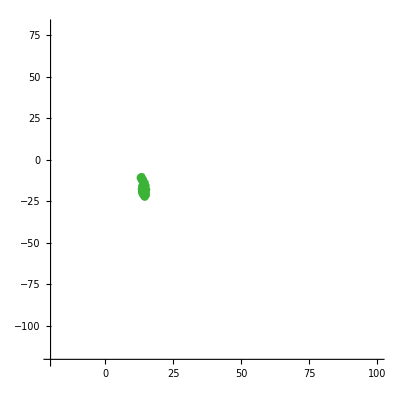
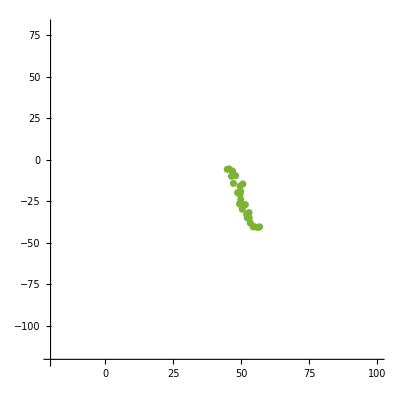
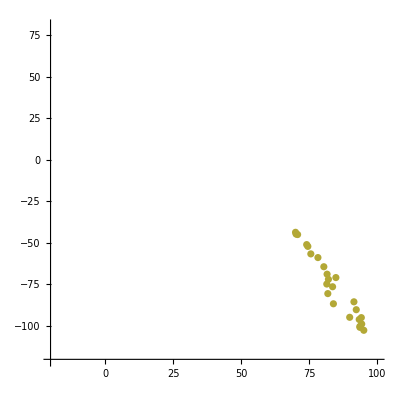
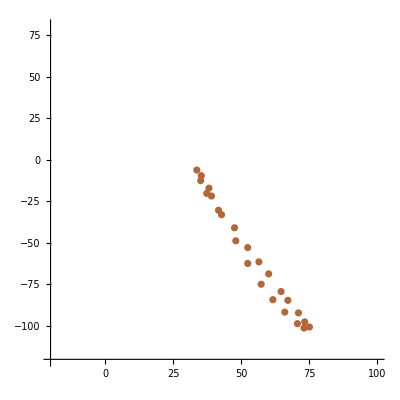
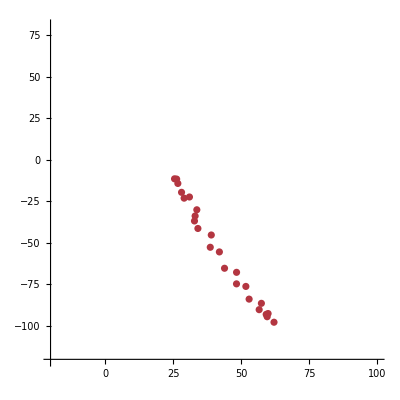
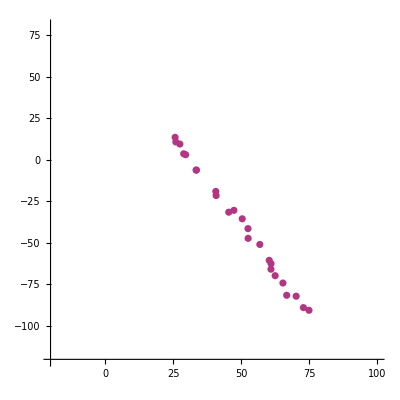
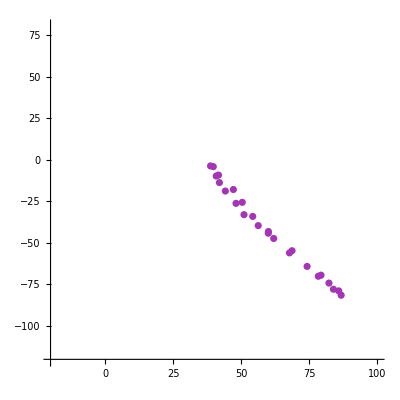

```mathematica
pcycles= Table[ListPlot[co2o2[[m]],  PlotRange -> {{-20,100},{ -120, 80}}, AxesOrigin -> {-20, - 120}, PlotStyle -> col[[m]], AspectRatio -> 1 , AxesStyle -> Directive[Black, 14, Thickness[0.005]]], {m, nm}]
```

```mathematica
coltab
```

Feb | Mar | Apr | May | Jun | Jul | Aug | Sep | Oct | Nov | Dec
RGBColor[0.21176470588235294, 0.7019607843137254, 0.4392156862745098] | RGBColor[0.23137254901960785, 0.7019607843137254, 0.21176470588235294] | RGBColor[0.48627450980392156, 0.7019607843137254, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.6588235294117647, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.403921568627451, 0.21176470588235294] | RGBColor[0.7019607843137254, 0.21176470588235294, 0.2549019607843137] | RGBColor[0.7019607843137254, 0.21176470588235294, 0.5098039215686274] | RGBColor[0.6352941176470588, 0.21176470588235294, 0.7019607843137254] | RGBColor[0.3843137254901961, 0.21176470588235294, 0.7019607843137254] | RGBColor[0.21176470588235294, 0.2901960784313726, 0.7019607843137254] | RGBColor[0.21176470588235294, 0.5450980392156862, 0.7019607843137254]

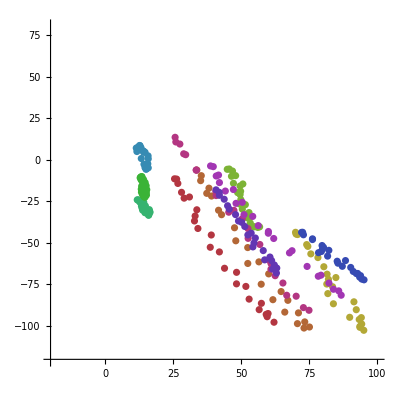

```mathematica
scycles = Show[pcycles]
```

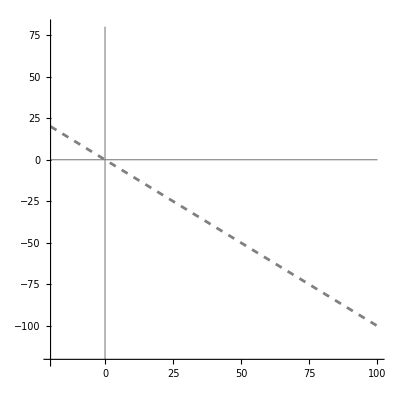

```mathematica
linp = Show[{ListPlot[{{-20,20}, {100, -100}},  PlotRange -> {{-20,100},{ -120,80}}, AxesOrigin -> {-20, -120}, 
PlotStyle -> {Gray,Dashed},  Joined -> True, AspectRatio -> 1 , AxesStyle -> Directive[Black, 14, Thickness[0.005]]], ListPlot[{{-20, 0},{100, 0}} , Joined -> True, PlotStyle -> {Gray, Thickness -> 0.002}], ListPlot[{{0, -120},{0, 80}} , Joined -> True, PlotStyle -> {Gray, Thickness -> 0.002}]}]
```

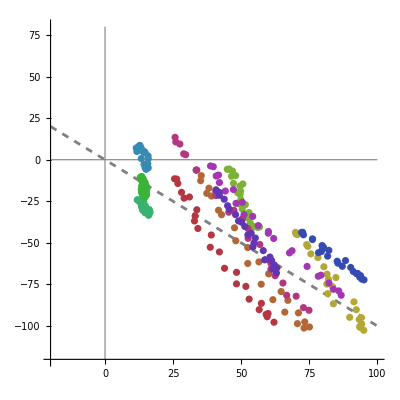

```mathematica
lcycles = Show[linp, scycles]
```

## Calculate average daily amplitudes

MinMax extracts the minimum and maximum values of a list as {min, max}. The difference max-min is the average daily amplitude.

```mathematica
diffco2 = Table[MinMax[Transpose[co2o2[[m]]][[1]]][[2]]- MinMax[Transpose[co2o2[[m]]][[1]]][[1]], {m, nm}]
```

{4.7063,2.42601,11.8683,25.0553,41.3281,36.5101,49.142,47.9485,22.2858,22.9243,4.40011}

```mathematica
diffo2 = Table[MinMax[Transpose[co2o2[[m]]][[2]]][[2]]- MinMax[Transpose[co2o2[[m]]][[2]]][[1]], {m, nm}]
```

{9.27197,12.402,35.0917,58.908,94.9778,86.2134,103.98,77.7185,50.0436,28.5628,14.3131}

```mathematica
difftab = Grid[{Prepend[mlabels,"Month"], Prepend[diffco2, "AmpCO2"], Prepend[diffo2, "AmpO2"]}, Dividers -> {False,All}]
```

Month | Feb | Mar | Apr | May | Jun | Jul | Aug | Sep | Oct | Nov | Dec
AmpCO2 | 4.7063 | 2.42601 | 11.8683 | 25.0553 | 41.3281 | 36.5101 | 49.142 | 47.9485 | 22.2858 | 22.9243 | 4.40011
AmpO2 | 9.27197 | 12.402 | 35.0917 | 58.908 | 94.9778 | 86.2134 | 103.98 | 77.7185 | 50.0436 | 28.5628 | 14.3131

## Calculate slopes of average 24 - h cycles

calculate the linear regression fits of the monthly averaged 24 - h co2 - o2 cycles with co2 as parameter x1 and extract the slope and intercept parameters , the extraction pattern ext is mapped over fitlist.

```mathematica
fitlist = Table[Fit[co2o2[[m]],{1, x1}, x1] ,{m, nm}]
```

{-1.6007-1.86516 x1,24.41-2.91357 x1,154.461-3.53623 x1,115.45-2.27972 x1,67.5665-2.31706 x1,46.1549-2.38062 x1,67.0177-2.13752 x1,52.44-1.56372 x1,70.4546-2.17468 x1,43.3644-1.21332 x1,42.9663-2.93637 x1}

```mathematica
ext = {#[[1]], #[[2]][[1]]}&
```

{#1⟦1⟧,#1⟦2⟧⟦1⟧}&

```mathematica
fitpar = ext/@fitlist
```

{{-1.6007,-1.86516},{24.41,-2.91357},{154.461,-3.53623},{115.45,-2.27972},{67.5665,-2.31706},{46.1549,-2.38062},{67.0177,-2.13752},{52.44,-1.56372},{70.4546,-2.17468},{43.3644,-1.21332},{42.9663,-2.93637}}

```mathematica
fittab = Grid[{Prepend[mlabels, "Month"], Prepend[Transpose[fitpar][[1]],"intercept"],  Prepend[Transpose[fitpar][[2]], "slope"]}, Dividers -> {False,All}]
```

Month | Feb | Mar | Apr | May | Jun | Jul | Aug | Sep | Oct | Nov | Dec
intercept | -1.6007 | 24.41 | 154.461 | 115.45 | 67.5665 | 46.1549 | 67.0177 | 52.44 | 70.4546 | 43.3644 | 42.9663
slope | -1.86516 | -2.91357 | -3.53623 | -2.27972 | -2.31706 | -2.38062 | -2.13752 | -1.56372 | -2.17468 | -1.21332 | -2.93637

## Visualize slopes

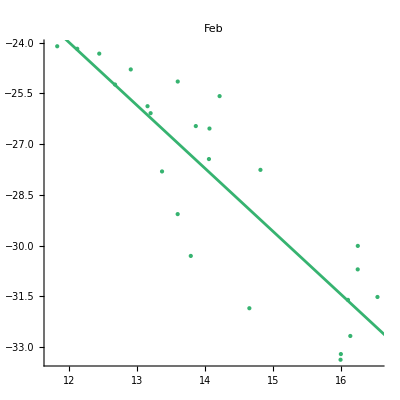
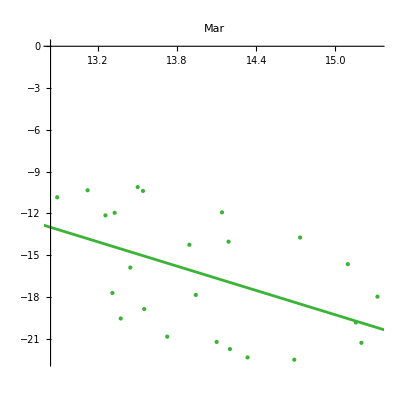
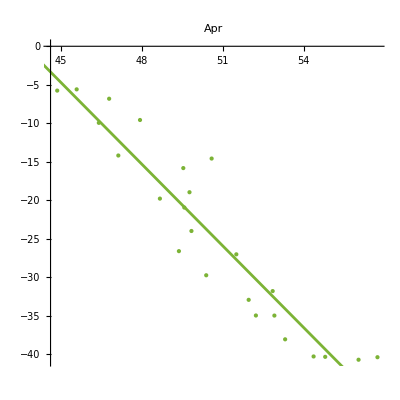
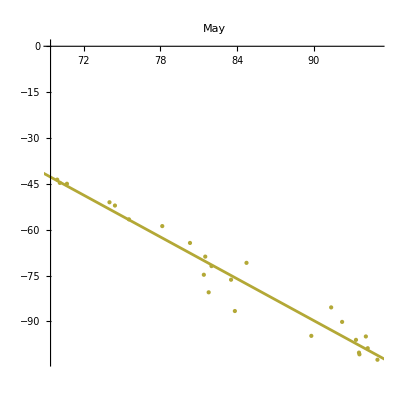
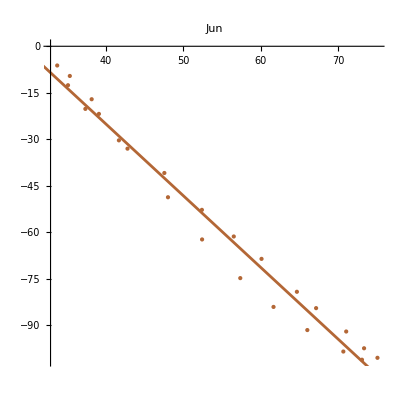
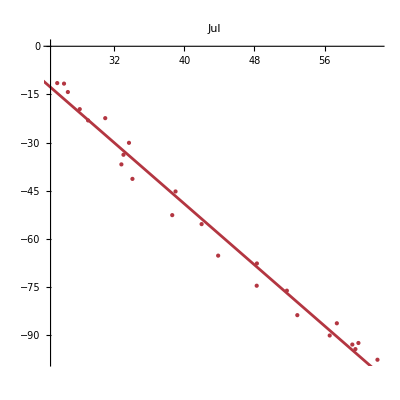
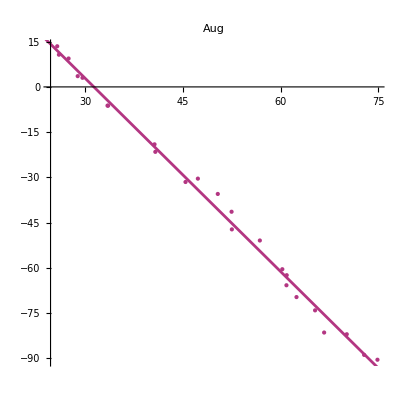
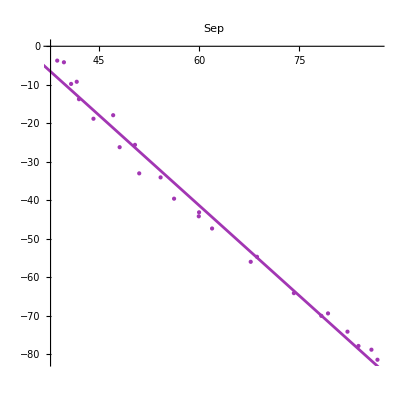

```mathematica
sloplots = Table[Show[{ListPlot[co2o2[[m]],   PlotStyle -> {col[[m]],PointSize -> Medium}, PlotLabel -> mlabels[[m]], AspectRatio -> 1 ], Plot[fitpar[[m,1]] + fitpar[[m,2]] y1, {y1, 0, 100}, PlotStyle -> col[[m]], AspectRatio -> 1]}],{m, nm}]
```

(END of CO2-O2-stat v1 notebook)